## Recurrence relations for SPT kernels (Carlson et al., 0905.0479)

Definitions for generic momenta q_1,...,q_n:

```mathematica
ClearAll[qs,qSel,qSum];
qs[n_]:=Table[q[m],{m,1,n}];
qSel[arr_,n1_,n2_]:=Take[arr,{n1,n2}]
qSum[arr_,n1_,n2_]:=Sum[arr[[nn]],{nn,n1,n2}]
```

The kernels: KerN[n,...][[1]]=F_n(...), KerN[n,...][[2]]=G_n(...).

```mathematica
ClearAll[KerN];
KerN[n_,arr_]:=Module[{k,k1,k2},
k=(qSum[arr,1,n]);
k1[m_]:=(qSum[arr,1,m]);
k2[m_]:=(qSum[arr,m+1,n]);
{
Sum[(KerN[m,qSel[arr,1,m]][[2]])/((2n+3)(n-1))((1+2n)(k.k1[m])/(k1[m].k1[m])KerN[n-m,qSel[arr,m+1,n]][[1]]+((k.k)(k1[m].k2[m]))/((k1[m].k1[m])(k2[m].k2[m]))KerN[n-m,qSel[arr,m+1,n]][[2]]),{m,1,n-1}],
Sum[(KerN[m,qSel[arr,1,m]][[2]])/((2n+3)(n-1))(3(k.k1[m])/(k1[m].k1[m])KerN[n-m,qSel[arr,m+1,n]][[1]]+n((k.k)(k1[m].k2[m]))/((k1[m].k1[m])(k2[m].k2[m]))KerN[n-m,qSel[arr,m+1,n]][[2]]),{m,1,n-1}]
}
];
KerN[1,a_]={1,1};
```

```mathematica
KerNSym[n_,arr_]:=Total[((KerN[n,#1]&)/@Permutations[arr])/(n!)]
```

```mathematica
F2[arr_]:=KerNSym[2,arr][[1]];
F3[arr_]:=KerNSym[3,arr][[1]];
G2[arr_]:=KerNSym[2,arr][[2]];
G3[arr_]:=KerNSym[3,arr][[2]];
```

### Petrubation Theory Kernels

```mathematica
perm12=Permutations[{q1,q2}];
perm123=Permutations[{q1,q2,q3}];
perm1234=Permutations[{q1,q2,q3,q4}];
```

```mathematica
Clear[Fn,Gn,n,m];
Fn[n_,v_]=If[n==1,1,Sum[Gn[m,v[[1;;m]]]/((2n+3)(n-1))((2n+1)al[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Fn[n-m,v[[m+1;;n]]]+2be[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Gn[n-m,v[[m+1;;n]]]),{m,1,n-1}]];
Gn[n_,v_]=If[n==1,1,Sum[Gn[m,v[[1;;m]]]/((2n+3)(n-1))(3al[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Fn[n-m,v[[m+1;;n]]]+2n be[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Gn[n-m,v[[m+1;;n]]]),{m,1,n-1}]];
```

```mathematica
F2s[q1_,q2_]=Simplify[Sum[1/Length[perm12]Fn[2,{perm12[[i,1]],perm12[[i,2]]}],{i,1,Length[perm12]}]];
F3s[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123]Fn[3,{perm123[[i,1]],perm123[[i,2]],perm123[[i,3]]}],{i,1,Length[perm123]}]];
F4s[q1_,q2_,q3_,q4_]=Simplify[Sum[1/Length[perm1234]Fn[4,{perm1234[[i,1]],perm1234[[i,2]],perm1234[[i,3]],perm1234[[i,4]]}],{i,1,Length[perm1234]}]];
```

```mathematica
alf[k1_,k2_]=(k1+k2).k1/(k1.k1);
bef[k1_,k2_]=(k1+k2).(k1+k2)(k1.k2)/2/(k1.k1)/(k2.k2) ;
alfm[k1_,k2_]=1+1/2(mag[k1+k2]^2-mag[k1]^2-mag[k2]^2)/mag[k1]^2;
befm[k1_,k2_]=(mag[k1+k2]^2(mag[k1+k2]^2-mag[k1]^2-mag[k2]^2))/(4 mag[k1]^2 mag[k2]^2);
sigma2[k1_,k2_]=1/4((mag[k1+k2]^2-mag[k1]^2-mag[k2]^2)^2)/(mag[k1]^2 mag[k2]^2)-1;
```

```mathematica
Gal3[k1_,k2_,k3_]:=-1/2(1-3((mag[k1+k2]^2-mag[k1]^2-mag[k2]^2)^2)/(4 mag[k1]^2 mag[k2]^2)+ ((mag[k1+k2]^2-mag[k1]^2-mag[k2]^2)(mag[k1+k3]^2-mag[k1]^2-mag[k3]^2)(mag[k3+k2]^2-mag[k3]^2-mag[k2]^2))/(4 mag[k1]^2 mag[k2]^2 mag[k3]^2));
```

## 1-Loop integral

### (c̃)_i parameters and (ĉ)_i kernels (see Appendix A)

initialize values

```mathematica
adelta={0,0,0,0,0,0,0,0,0,0};
btheta={0,0,0,0,0,0,0,0,0,0};
a0={0,0,0,0,0,0,0,0,0,0,0,0,0};
b0={0,0,0,0,0,0,0,0,0,0,0,0,0};
```

```mathematica
biasA={0,0,0,0,0};
biasB={0,0,0,0,0};
biasA⟦1⟧="(b^A)_(δ, 1)";
biasA⟦2⟧="(b^A)_(δ, 2)";
biasA⟦3⟧="(b^A)_(δ, 3)";
biasA⟦4⟧="(b^A)_(δ^2)";
biasA⟦5⟧="(b^A)_c_s";

biasB⟦1⟧="(b^B)_(δ, 1)";
biasB⟦2⟧="(b^B)_(δ, 2)";
biasB⟦3⟧="(b^B)_(δ, 3)";
biasB⟦4⟧="(b^B)_(δ^2)";
biasB⟦5⟧="(b^B)_c_s";
```

```mathematica
adelta⟦1⟧="((c̃)^A)_(δ, 1)";
adelta⟦2⟧="((c̃)^A)_(δ, 2 (2))";
adelta⟦3⟧="((c̃)^A)_(δ, 2 (3))";
adelta⟦4⟧="((c̃)^A)_(δ, 3)";
adelta⟦5⟧="((c̃)^A)_(δ, 3 SubscriptBox[c, s])";
adelta⟦6⟧="((c̃)^A)_(δ^2)";
adelta⟦7⟧="((c̃)^A)_(δ^2)";
adelta⟦8⟧="((c̃)^A)_(δ^2)";
adelta⟦9⟧="((c̃)^A)_(s^2)";
adelta⟦10⟧="((c̃)^A)_(δ^3)";

a0⟦1⟧="(c^A)_(δ, 1)";
a0⟦2⟧="(c^A)_(δ, 2)";
a0⟦3⟧="(c^A)_(δ, 3)";
a0⟦4⟧="(c^A)_(δ, 3 SubscriptBox[c, s])";
a0⟦5⟧="(c^A)_(δ^2)";
a0⟦6⟧="(c^A)_(δ^2)";
a0⟦7⟧="(c^A)_(δ^3)";
a0⟦8⟧="(c^A)_(s^2)";
a0⟦9⟧="(c^A)_(s^2)";
a0⟦10⟧="(c^A)_(s^3)";
a0⟦11⟧="(c^A)_(st, 1)";
a0⟦12⟧="(c^A)_(ψ, 1)";
a0⟦13⟧="(c^A)_(δs^2)";

btheta⟦1⟧="((c̃)^B)_(δ, 1)";
btheta⟦2⟧="((c̃)^B)_(δ, 2 (2))";
btheta⟦3⟧="((c̃)^B)_(δ, 2 (3))";
btheta⟦4⟧="((c̃)^B)_(δ, 3)";
btheta⟦5⟧="((c̃)^B)_(δ, 3 SubscriptBox[c, s])";
btheta⟦6⟧="((c̃)^B)_(δ^2)";
btheta⟦7⟧="((c̃)^B)_(δ^2)";
btheta⟦8⟧="((c̃)^B)_(δ^2)";
btheta⟦9⟧="((c̃)^B)_(s^2)";
btheta⟦10⟧="((c̃)^B)_(δ^3)";
```

```mathematica
b0⟦1⟧="(c^B)_(δ, 1)";
b0⟦2⟧="(c^B)_(δ, 2)";
b0⟦3⟧="(c^B)_(δ, 3)";
b0⟦4⟧="(c^B)_(δ, 3 SubscriptBox[c, s])";
b0⟦5⟧="(c^B)_(δ^2)";
b0⟦6⟧="(c^B)_(δ^2)";
b0⟦7⟧="(c^B)_(δ^3)";
b0⟦8⟧="(c^B)_(s^2)";
b0⟦9⟧="(c^B)_(s^2)";
b0⟦10⟧="(c^B)_(s^3)";
b0⟦11⟧="(c^B)_(st, 1)";
b0⟦12⟧="(c^B)_(ψ, 1)";
b0⟦13⟧="(c^B)_(δs^2)";
```

```mathematica
Clear[c1]
c1=Subscript["(ĉ)^(1)","δ,1"];
```

```mathematica
c2={0,0,0,0};
c2⟦1⟧=Subscript["(ĉ)^(2)","δ,1"];
c2⟦2⟧=Subscript["(ĉ)^(2)","δ,2"];
c2⟦3⟧=Subscript["(ĉ)^(2)","δ^2,1"];
c2⟦4⟧=Subscript["(ĉ)^(2)","s^2,1"];
```

```mathematica
c3={0,0,0,0,0,0,0,0,0,0,0,0};
c3⟦1⟧=Subscript["(ĉ)^(3)","δ,1"];
c3⟦2⟧=Subscript["(ĉ)^(3)","δ,2"];
c3⟦3⟧=Subscript["(ĉ)^(3)","δ,3"];
c3⟦4⟧=Subscript["(ĉ)^(3)","δ^2,1"];
c3⟦5⟧=Subscript["(ĉ)^(3)","δ^2,2"];
c3⟦6⟧=Subscript["(ĉ)^(3)","δ^3"];
c3⟦7⟧=Subscript["(ĉ)^(3)","s^2,1"];
c3⟦8⟧=Subscript["(ĉ)^(3)","s^2,2"];
c3⟦9⟧=Subscript["(ĉ)^(3)","s^3"];
c3⟦10⟧=Subscript["(ĉ)^(3)","st"];
c3⟦11⟧=Subscript["(ĉ)^(3)","ψ"];
c3⟦12⟧=Subscript["(ĉ)^(3)","δs^2"];
```

```mathematica
Clear[asub];
```

definitions of parameters in basis of descendents

```mathematica
asub[a_,a0_]:={a⟦1⟧->a0⟦1⟧,a⟦2⟧->a0⟦2⟧+7/2 a0⟦8⟧,a⟦3⟧->a0⟦2⟧+7/2 a0⟦8⟧,a⟦4⟧->a0⟦3⟧+45/4 a0⟦10⟧+9/2 a0⟦11⟧+2a0⟦12⟧,a⟦5⟧->a0⟦4⟧,a⟦6⟧->a0⟦5⟧-17/6 a0⟦8⟧,a⟦7⟧->a0⟦5⟧-17/6 a0⟦8⟧ , a⟦8⟧->a0⟦6⟧-137/16 a0⟦10⟧-71/24 a0⟦11⟧-55/42 a0⟦12⟧+7/4 a0⟦13⟧, a⟦9⟧->a0⟦9⟧-3/4 a0⟦10⟧-1/2 a0⟦11⟧-2/7 a0⟦12⟧, a⟦10⟧->a0⟦7⟧+511/72 a0⟦10⟧+25/12 a0⟦11⟧+a0⟦12⟧-17/6 a0⟦13⟧};
```

```mathematica
asub[adelta,a0]
```

{((c̃)^A)_(δ, 1)→(c^A)_(δ, 1),((c̃)^A)_(δ, 2 (2))→(7 (c^A)_(s^2))/2+(c^A)_(δ, 2),((c̃)^A)_(δ, 2 (3))→(7 (c^A)_(s^2))/2+(c^A)_(δ, 2),((c̃)^A)_(δ, 3)→(9 (c^A)_(st, 1))/2+(45 (c^A)_(s^3))/4+(c^A)_(δ, 3)+2 (c^A)_(ψ, 1),((c̃)^A)_(δ, 3 SubscriptBox[c, s])→(c^A)_(δ, 3 SubscriptBox[c, s]),((c̃)^A)_(δ^2)→-(17 (c^A)_(s^2))/6+(c^A)_(δ^2),((c̃)^A)_(δ^2)→-(17 (c^A)_(s^2))/6+(c^A)_(δ^2),((c̃)^A)_(δ^2)→-(71 (c^A)_(st, 1))/24-(137 (c^A)_(s^3))/16+(c^A)_(δ^2)+(7 (c^A)_(δs^2))/4-(55 (c^A)_(ψ, 1))/42,((c̃)^A)_(s^2)→-((c^A)_(st, 1))/2+(c^A)_(s^2)-(3 (c^A)_(s^3))/4-(2 (c^A)_(ψ, 1))/7,((c̃)^A)_(δ^3)→(25 (c^A)_(st, 1))/12+(511 (c^A)_(s^3))/72+(c^A)_(δ^3)-(17 (c^A)_(δs^2))/6+(c^A)_(ψ, 1)}

```mathematica
b0ThetaValues=asub[btheta,b0]/.Join[Thread[b0⟦1;;3⟧->1],{b0⟦12⟧->1},Thread[b0⟦5;;6⟧->-4/21],{b0⟦7⟧->0},Thread[b0⟦8;;9⟧->2/7],Thread[b0⟦10;;11⟧->0],{b0⟦13⟧->0}]
```

{((c̃)^B)_(δ, 1)→1,((c̃)^B)_(δ, 2 (2))→2,((c̃)^B)_(δ, 2 (3))→2,((c̃)^B)_(δ, 3)→3,((c̃)^B)_(δ, 3 SubscriptBox[c, s])→(c^B)_(δ, 3 SubscriptBox[c, s]),((c̃)^B)_(δ^2)→-1,((c̃)^B)_(δ^2)→-1,((c̃)^B)_(δ^2)→-3/2,((c̃)^B)_(s^2)→0,((c̃)^B)_(δ^3)→1}

expressions for ĉ kernels

```mathematica
c1[q1_]:=1;

c2⟦1⟧[q1_,q2_]:=(q1.q2)/(q1.q1);
c2⟦2⟧[q1_,q2_]:=F2[{q1,q2}]-(q1.q2)/(q1.q1);
c2⟦3⟧[q1_,q2_]:=1;
c2⟦4⟧[q1_,q2_]:=(q1.q2)^2/((q1.q1)(q2.q2))-1/3;

c3⟦1⟧[q1_,q2_,q3_]:=1/2((q1.q2+q1.q3)/((q2+q3).(q2+q3))G2[{q2,q3}]+((q1.q2)(q1.q3+q2.q3))/((q2.q2)(q3.q3)));
c3⟦2⟧[q1_,q2_,q3_]:=(q1.q3+q2.q3)/((q2.q2)(q3.q3))(F2[{q1,q2}](q2.q2)-q1.q2);
c3⟦3⟧[q1_,q2_,q3_]:=F3[{q1,q2,q3}]+((q1+q2).q3)/(2 (q2.q2)(q3.q3))(q1.q2-2 F2[{q1,q2}](q2.q2))-(q1.(q2+q3))/(2(q2+q3).(q2+q3))G2[{q2,q3}];
c3⟦4⟧[q1_,q2_,q3_]:=2 (q2.q3)/(q3.q3);
c3⟦5⟧[q1_,q2_,q3_]:=2F2[{q1,q2}]-2(q2.q3)/(q3.q3);
c3⟦6⟧[q1_,q2_,q3_]:=1;
c3⟦7⟧[q1_,q2_,q3_]:=2 (q2.q3)/(q3.q3)((q1.q2)^2/((q1.q1)(q2.q2))-1/3);
c3⟦8⟧[q1_,q2_,q3_]:=2F2[{q1,q2}](((q1+q2).q3)^2/((q1+q2).(q1+q2)(q3.q3))-1/3)-2(q2.q3)/(q3.q3)((q1.q2)^2/((q1.q1)(q2.q2))-1/3);
c3⟦9⟧[q1_,q2_,q3_]:=1/(9(q1.q1)(q2.q2)(q3.q3))(9(q1.q2)(q2.q3)(q1.q3)-3(q1.q3)^2(q2.q2)-3(q1.q2)^2(q3.q3)+(q1.q1)(-3(q2.q3)^2+2(q2.q2)(q3.q3)));
c3⟦10⟧[q1_,q2_,q3_]:=(G2[{q1,q2}]-F2[{q1,q2}])(((q1+q2).q3)^2/((q1+q2).(q1+q2)(q3.q3))-1/3);
c3⟦11⟧[q1_,q2_,q3_]:=G3[{q1,q2,q3}]-F3[{q1,q2,q3}]+2F2[{q1,q2}](F2[{q1+q2,q3}]-G2[{q1+q2,q3}]);
c3⟦12⟧[q1_,q2_,q3_]:=(q1.q2)^2/((q1.q1)(q2.q2))-1/3;
cn={c1,c2,c3};
```

### halo kernels in redshift space (see Appendices B and C)

vector substitutions for k, q, and z-hat

```mathematica
kqsub={k-> kk{0,0,1},q-> {qq √(1-x^2) α,qq √(1-x^2) √(1-α^2),qq x}}//Simplify;
zhat = {√(1-μ^2),0,μ};
```

define symmetrization over two and three variables

```mathematica
q2sym[f_,q1_,q2_]:=1/2(f[q1,q2]+f[q2,q1]);
q3sym[f_,q1_,q2_,q3_]:=1/6(f[q1,q2,q3]+f[q1,q3,q2]+f[q2,q3,q1]+f[q2,q1,q3]+f[q3,q2,q1]+f[q3,q1,q2]);
```

```mathematica
Clear[k,q,aa,bb]
```

```mathematica
subs3[func_,kk_,qq_,x_]:=((q3sym[func,q1,q2,q3]/.{q2+q3->ϵ}/.{q1->k,q2->-q,q3->q}/.{ϵ.ϵ->ϵ0^2}/.{k+ϵ->k}//.{Dot[aa_,-bb_]->-Dot[aa,bb],Dot[-aa_,bb_]->-Dot[aa,bb]}//Simplify)//.{Dot[aa_,ϵ]->0,Dot[ϵ,aa_]->0,ϵ0->0}/.kqsub//Simplify)
```

```mathematica
finduv3[func_,num_]:=Integrate[Series[subs3[func[[num]],kk,qq,x],{qq,∞,0}]//Normal,{x,-1,1}]//Simplify
testuv3[func_,num_]:=Series[subs3[func[[num]],kk,qq,x],{qq,∞,2}];
testuv3alpha[func_,num_]:=subs3[func[[num]],kk,qq,x];
```

```mathematica
c3uv=finduv3[c3,#]&/@Table[i,{i,1,Length[c3]}];
```

```mathematica
Clear[c3ir,c2ir]
```

```mathematica
c3ir[kk_,qq_,x_]=Table[subs3[c3[[i]],kk,qq,x]-1/2 c3uv[[i]],{i,1,Length[c3]}]//Simplify
```

{13/63+(-7 kk^6 x^2+28 kk^4 qq^2 x^2 (-1+x^2)-2 qq^6 (3+4 x^2)+kk^2 qq^4 (-6-17 x^2+44 x^4))/(42 qq^2 (kk^2+qq^2-2 kk qq x) (kk^2+qq^2+2 kk qq x)),-4/63 (-1+3 x^2),-(4 (2 qq^4 (1-3 x^2)+kk^4 (3-8 x^2+x^4)+kk^2 qq^2 (5-22 x^2+25 x^4)))/(63 (kk^2+qq^2-2 kk qq x) (kk^2+qq^2+2 kk qq x)),0,8/63 (-1+3 x^2),0,2/9-(2 x^2)/3,-(2 (29 qq^4 (1-3 x^2)+kk^4 (119-267 x^2+90 x^4)+2 kk^2 qq^2 (74-235 x^2+219 x^4)))/(189 (kk^2+qq^2-2 kk qq x) (kk^2+qq^2+2 kk qq x)),1/9 (-1+3 x^2),4/189 (4+(3 (-1+x^2) (2 qq^4+kk^2 qq^2 (1-5 x^2)+kk^4 (-1+3 x^2)))/((kk^2+qq^2-2 kk qq x) (kk^2+qq^2+2 kk qq x))),(64 kk^2 (kk^2+qq^2) (-1+x^2)^2)/(441 (kk^2+qq^2-2 kk qq x) (kk^2+qq^2+2 kk qq x)),2/9 (-1+3 x^2)}

```mathematica
c2ir[kk_,qq_,x_]=Table[(q2sym[c2[[i]],q1,q2]/.{q1->k-q,q2->q}/.kqsub//Simplify),{i,1,Length[c2]}]//Simplify;

c2irneg[kk_,qq_,x_]=Table[(q2sym[c2[[i]],q1,q2]/.{q1->k+q,q2->-q}/.kqsub//Simplify),{i,1,Length[c2]}]//Simplify;
```

```mathematica
ker1[aa_]:=aa[[1]];
```

Halo Kernels - The aa will be adelta

```mathematica
K2[q1_,q2_,aa_]:=aa⟦1⟧ c2⟦1⟧[q1,q2]+aa⟦2⟧ c2⟦2⟧[q1,q2]+aa⟦6⟧ c2⟦3⟧[q1,q2];
K3[q1_,q2_,q3_,aa_]:=aa⟦1⟧ c3⟦1⟧[q1,q2,q3]+aa⟦3⟧ c3⟦2⟧[q1,q2,q3]+aa⟦4⟧ c3⟦3⟧[q1,q2,q3]+aa⟦7⟧ c3⟦4⟧[q1,q2,q3]+aa⟦8⟧ c3⟦5⟧[q1,q2,q3]+aa⟦10⟧ c3⟦6⟧[q1,q2,q3]+aa⟦9⟧ c3⟦8⟧[q1,q2,q3] ;
```

UV-subtracted Halo Kernels - The aa will be adelta

```mathematica
K2ir[kk_,qq_,x_,aa_]:=aa⟦1⟧ c2ir[kk,qq,x]⟦1⟧+aa⟦2⟧ c2ir[kk,qq,x]⟦2⟧+aa⟦6⟧ c2ir[kk,qq,x]⟦3⟧;
K3ir[kk_,qq_,x_,aa_]:=aa⟦1⟧ c3ir[kk,qq,x]⟦1⟧+aa⟦3⟧ c3ir[kk,qq,x]⟦2⟧+aa⟦4⟧ c3ir[kk,qq,x]⟦3⟧+aa⟦7⟧ c3ir[kk,qq,x]⟦4⟧+aa⟦8⟧ c3ir[kk,qq,x]⟦5⟧+aa⟦10⟧ c3ir[kk,qq,x]⟦6⟧+aa⟦9⟧ c3ir[kk,qq,x]⟦8⟧
```

Second-order redshift-space halo kernels

```mathematica
K2rIR[kk_,qq_,x_,μ_]:=K2ir[kk,qq,x,adelta]+f1 μ^2 K2ir[kk,qq,x,btheta]+μ f1 kk 1/2((q1.zhat)/(q1.q1)+(q2.zhat)/(q2.q2))ker1[btheta]ker1[adelta]+1/2 μ^2 f1^2 kk^2 ((q1.zhat)(q2.zhat))/((q1.q1)(q2.q2))ker1[btheta]ker1[btheta]/.{q1->k-q,q2->q}/.kqsub;
```

additional third-order kernels for haloes redshift space

```mathematica
keruv={0,0,0,0,0};
```

```mathematica
ker1[q1_,q2_,q3_]:=kk^2(q1.zhat)/(q1.q1)(q2.zhat)/(q2.q2)ker1[btheta]ker1[btheta]ker1[adelta];
ker1sym[kk_,qq_,x_]=q3sym[ker1,q1,q2,q3]/.{q1->k,q2->-q,q3->q}/.kqsub//Simplify;
keruv[[1]]=Series[ker1sym[kk,qq,x],{qq,∞,0}]//Normal;
```

```mathematica
ker2[q1_,q2_,q3_]=kk^3(q1.zhat)/(q1.q1)(q2.zhat)/(q2.q2)(q3.zhat)/(q3.q3)ker1[btheta]ker1[btheta]ker1[btheta];
ker2sym[kk_,qq_,x_]=q3sym[ker2,q1,q2,q3]/.{q1->k,q2->-q,q3->q}/.kqsub//Simplify;
keruv[[2]]=Series[ker2sym[kk,qq,x],{qq,∞,0}]//Normal;
```

```mathematica
ker3[q1_,q2_,q3_]=kk(q1.zhat+q2.zhat)/((q1+q2).(q1+q2))K2[q1,q2,btheta]ker1[adelta];
ker3sym[kk_,qq_,x_]=q3sym[ker3,q1,q2,q3]/.{q1->k,q2->-q,q3->q}/.kqsub//Simplify;
keruv[[3]]=Integrate[Series[ker3sym[kk,qq,x],{qq,∞,0}]//Normal,{x,-1,1}];
```

```mathematica
ker4[q1_,q2_,q3_]=kk^2(q1.zhat+q2.zhat)/((q1+q2).(q1+q2))(q3.zhat)/(q3.q3)K2[q1,q2,btheta]ker1[btheta] ;
ker4sym[kk_,qq_,x_]=q3sym[ker4,q1,q2,q3]/.{q1->k,q2->-q,q3->q}/.kqsub//Simplify;keruv[[4]]=Series[ker4sym[kk,qq,x],{qq,∞,0}]//Normal
```

0

```mathematica
ker5[q1_,q2_,q3_]=kk(q3.zhat)/(q3.q3)K2[q1,q2,adelta]ker1[btheta];
ker5sym[kk_,qq_,x_]=q3sym[ker5,q1,q2,q3]/.{(q2+q3).aa_->0}/.{q1->k,q2->-q,q3->q}/.kqsub//Simplify;
keruv[[5]]=Integrate[Series[ker5sym[kk,qq,x],{qq,∞,0}]//Normal,{x,-1,1}]//Simplify;
```

Third-order redshift-space halo kernel

```mathematica
K3r[kk_,qq_,x_,μ_]:=K3ir[kk,qq,x,adelta]+f1 μ^2 K3ir[kk,qq,x,btheta]+f1^2/2 μ^2 (ker1sym[kk,qq,x]-1/2 keruv[[1]])+f1^3/6 μ^3(ker2sym[kk,qq,x]-1/2 keruv[[2]])+f1 μ ( ker3sym[kk,qq,x]-1/2 keruv[[3]])+f1^2 μ^2(ker4sym[kk,qq,x]-1/2 keruv[[4]])+f1 μ ( ker5sym[kk,qq,x]-1/2 keruv[[5]]);

K3rIR[kk_,qq_,x_,μ_]=K3r[kk,qq,x,μ]-1/2 Integrate[Series[K3r[kk,qq,x,μ],{qq,∞,2}]//Normal,{x,-1,1}];
```

### 1-Loop integrands

define bias parameters

```mathematica
tb={adelta⟦1⟧->biasA⟦1⟧,adelta⟦6⟧->biasA⟦4⟧,adelta⟦2⟧->biasA⟦2⟧,adelta⟦4⟧->(-15adelta⟦9⟧+biasA⟦3⟧)};
tosym={biasA⟦1⟧->b1,biasA⟦2⟧->b2,biasA⟦3⟧->b3,biasA⟦4⟧->b4,biasA⟦5⟧->b5,Subscript[c, r1]->b6,Subscript[c, r2]->b7,Subscript[c, r3]->b8,Subscript[c, r4]->b9,Subscript[c, r5]->b10,Subscript[c, r6]->b11};
```

P^(22) integrand

```mathematica
PhhRIntegrand22[kk_,qq_,x_,μ_]=Series[Integrate[2*(K2rIR[kk,qq,x,μ])^2/.tb/.b0ThetaValues/.{α->Cos[ϕ]},{ϕ,0,2π}],{μ,0,10}]//Normal//Expand;
```

```mathematica
PhhRIntegrandExp22[kk_,qq_,x_]=Series[PhhRIntegrand22[kk,qq,x,μ],{μ,0,8}]//Normal//Expand;
```

P^(13) integrand

```mathematica
PhhRIntegrand13[kk_,qq_,x_,μ_]=Series[Integrate[6*(adelta[[1]]+f1 μ^2 btheta[[1]])K3rIR[kk,qq,x,μ]/.tb/.b0ThetaValues/.{α->Cos[ϕ]},{ϕ,0,2π}],{μ,0,10}]//Normal//Expand;
```

```mathematica
PhhRIntegrandExp13[kk_,qq_,x_]=Series[PhhRIntegrand13[kk,qq,x,μ],{μ,0,8}]//Normal//Expand;
```

Final Halo integrand

```mathematica
PhhRIntegrandFin13[kk_,qq_,x_]=PhhRIntegrandExp13[kk,qq,x]/.{biasB⟦1⟧->0}//Expand;
PhhRIntegrandFin22[kk_,qq_,x_]=PhhRIntegrandExp22[kk,qq,x]/.{biasB⟦1⟧->0}//Expand;
```

```mathematica
PhhRIntegrandAll13[kk_,qq_,x_,μ_]=PhhRIntegrand13[kk,qq,x,μ]/.{biasB⟦1⟧->0}//Expand;
PhhRIntegrandAll22[kk_,qq_,x_,μ_]=PhhRIntegrand22[kk,qq,x,μ]/.{biasB⟦1⟧->0}//Expand;
```

“Cosmology”-free Integrands: removing bias parameters, powers of μ^2 and f from the integrands

```mathematica
μlist={μ^2,μ^4,μ^6,μ^8};
clist1=Outer[Times,μlist,Outer[Times,biasA,biasA]]//Flatten//DeleteDuplicates;
clist2=Outer[Times,biasA,biasA]//Flatten//DeleteDuplicates;
clist3=Outer[Times,biasA,μlist]//Flatten//DeleteDuplicates;
fullclist=Join[clist1,clist2,clist3,μlist];
flist={1,f1,f1^2,f1^3,f1^4};
fullflist=Outer[Times,flist,fullclist]//Flatten;
```

```mathematica
(*P13: Factorizing out bias parameters and powers of μ*)
Clear[coef1,coef2,coef3,coefμ,Kernel,Kf0, Kf1, Kf2, Kf3, Kf4, Kfs]
coef1[kk_,qq_,x_]=Coefficient[PhhRIntegrandFin13[kk,qq,x],clist1];
coef2[kk_,qq_,x_]=Coefficient[PhhRIntegrandFin13[kk,qq,x]/.Thread[clist1->0],clist2];
coef3[kk_,qq_,x_]=Coefficient[PhhRIntegrandFin13[kk,qq,x]/.Thread[clist1->0]/.Thread[clist2->0],clist3];
coefμ[kk_,qq_,x_]=Coefficient[PhhRIntegrandFin13[kk,qq,x]/.Thread[biasA->0],μlist];
Kernel[kk_,qq_,x_]=Join[coef1[kk,qq,x],coef2[kk,qq,x],coef3[kk,qq,x],coefμ[kk,qq,x]];

(*Check that all coefficients are included in Kernel*)
Residual[x_]=PhhRIntegrandFin13[kk,qq,x]-Kernel[kk,qq,x].fullclist/.tb/.tosym//Expand//Simplify
Integrate[Residual[x],{x,-1,1}]
```

-8/63 (151 ((c̃)^A)_(s^2)+6 (-2 ((c̃)^A)_(δ^2)+((c̃)^A)_(δ, 2 (3)))) b1 π (-1+3 x^2)

0

```mathematica
(*Factorizing out powers of f*)
Kf1[kk_,qq_,x_] = Coefficient[Kernel[kk,qq,x],f1];
Kf2[kk_,qq_,x_] = Coefficient[Kernel[kk,qq,x],f1^2];
Kf3[kk_,qq_,x_] = Coefficient[Kernel[kk,qq,x],f1^3];
Kf4[kk_,qq_,x_] = Coefficient[Kernel[kk,qq,x],f1^4];
Kf0[kk_,qq_,x_] =Kernel[kk,qq,x]//.f1-> 0;
Kfs[kk_,qq_,x_]=Join[Kf0[kk,qq,x],Kf1[kk,qq,x],Kf2[kk,qq,x],Kf3[kk,qq,x],Kf4[kk,qq,x]];

(*Check that all coefficients are included in Kf's*)
Residual[x_]=PhhRIntegrandFin13[kk,qq,x]-Kfs[kk,qq,x].fullflist/.tb/.tosym;
Integrate[Residual[x],{x,-1,1}]
```

0

```mathematica
(*Sort and take out zeros*)
K13all =Kfs[k,q,x]//Simplify;
N13 = Length[K13all];
Kernel13 = {};
Coef13 = {};
For[i=1,i<=N13,i++, If[K13all[[i]]===0 ,,AppendTo[Kernel13, K13all[[i]]]  && AppendTo[Coef13, fullflist⟦i⟧]]];
Coef13/.tosym
```

```mathematica
{b1^2,b1 b3,b1^2 f1 μ^2,b1 f1 μ^2,b3 f1 μ^2,f1 μ^2,b1^2 f1^2 μ^2,b1^2 f1^2 μ^4,b1 f1^2 μ^2,b1 f1^2 μ^4,f1^2 μ^4,b1 f1^3 μ^4,b1 f1^3 μ^6,f1^3 μ^4,f1^3 μ^6,f1^4 μ^6,f1^4 μ^8}
```

```mathematica
(*P22: Factorizing out bias parameters and powers of μ*)
Clear[coef1,coef2,coef3,coefμ,Kernel,Kf0, Kf1, Kf2, Kf3, Kf4, Kfs]
coef1[kk_,qq_,x_,μ_]=Coefficient[PhhRIntegrandFin22[kk,qq,x],clist1];
coef2[kk_,qq_,x_,μ_]=Coefficient[PhhRIntegrandFin22[kk,qq,x]/.Thread[clist1->0],clist2];
coef3[kk_,qq_,x_,μ_]=Coefficient[PhhRIntegrandFin22[kk,qq,x]/.Thread[clist1->0]/.Thread[clist2->0],clist3];
coefμ[kk_,qq_,x_,μ_]=Coefficient[PhhRIntegrandFin22[kk,qq,x]/.Thread[biasA->0],μlist];
Kernel[kk_,qq_,x_]=Join[coef1[kk,qq,x,μ],coef2[kk,qq,x,μ],coef3[kk,qq,x,μ],coefμ[kk,qq,x,μ]];

(*Check that all coefficients are included in Kernel*)
PhhRIntegrandFin22[kk,qq,x]-Kernel[kk,qq,x].fullclist/.tb/.tosym//Expand//Simplify
```

0

```mathematica
(*Factorizing out powers of f*)
Kf1[kk_,qq_,x_] = Coefficient[Kernel[kk,qq,x],f1];
Kf2[kk_,qq_,x_] = Coefficient[Kernel[kk,qq,x],f1^2];
Kf3[kk_,qq_,x_] = Coefficient[Kernel[kk,qq,x],f1^3];
Kf4[kk_,qq_,x_] = Coefficient[Kernel[kk,qq,x],f1^4];
Kf0[kk_,qq_,x_] =Kernel[kk,qq,x]//.f1-> 0;
Kfs[kk_,qq_,x_]=Join[Kf0[kk,qq,x],Kf1[kk,qq,x],Kf2[kk,qq,x],Kf3[kk,qq,x],Kf4[kk,qq,x]];

(*Check that all coefficients are included in Kf's*)
PhhRIntegrandFin22[kk,qq,x]-Kfs[kk,qq,x].fullflist/.tb/.tosym//Expand//Simplify
```

0

```mathematica
(*Sort and take out zeros*)
K22all =Kfs[k,q,x]//Simplify;
N22 = Length[K22all];
Kernel22 = {};
Coef22 = {};
For[i=1,i<=N22,i++, If[K22all[[i]]===0,,AppendTo[Kernel22, K22all[[i]]]  && AppendTo[Coef22, fullflist[[i]]]]];
Coef22/.tosym
Length[Coef22]
```

{b1^2,b1 b2,b1 b4,b2^2,b2 b4,b4^2,b1^2 f1 μ^2,b1 b2 f1 μ^2,b1 b4 f1 μ^2,b1 f1 μ^2,b2 f1 μ^2,b4 f1 μ^2,b1^2 f1^2 μ^2,b1^2 f1^2 μ^4,b1 f1^2 μ^2,b1 f1^2 μ^4,b2 f1^2 μ^2,b2 f1^2 μ^4,b4 f1^2 μ^2,b4 f1^2 μ^4,f1^2 μ^4,b1 f1^3 μ^4,b1 f1^3 μ^6,f1^3 μ^4,f1^3 μ^6,f1^4 μ^4,f1^4 μ^6,f1^4 μ^8}

28

```mathematica
(* At the end of the day, you get the cosmology-free Kernel13 and Kernel22 with Coef13 and Coef22, respectively. *)
```

### 1-loop integrals by Dim. Reg.

Auxiliary function

```mathematica
J2[k_,ν1_,ν2_]:=1/(2π)^3(Gamma[3/2-ν1]Gamma[3/2-ν2]Gamma[ν1+ν2-3/2])/(Gamma[ν1]Gamma[ν2]Gamma[3-ν1-ν2])π^(3/2)k^(3-2ν1-2ν2);
```

```mathematica
FortranForm[(1/(2π)^3(Gamma[3/2-ν1]Gamma[3/2-ν2]Gamma[ν1+ν2-3/2])/(Gamma[ν1]Gamma[ν2]Gamma[3-ν1-ν2])π^(3/2)//Simplify)//.{ν1-> n1, ν2-> n2} ]/.{Gamma-> gamma}
```

(gamma(1.5 - n1)*gamma(1.5 - n2)*gamma(-1.5 + n1 + n2))/(8.*Pi**1.5*gamma(n1)*gamma(3 - n1 - n2)*gamma(n2))

Dim. Reg.

```mathematica
(* 13-diagram *)
Clear[P13];
(*
P13 = {} ;
Do[
Clear[Tab13,Integrand13];
Integrand13 =(( Kernel13[[j]]//Apart)/.{k^2+q^2-2 k q x-> kmq^2}/.{-k^2-q^2+2 k q x->- kmq^2}/.{k^2+q^2+2 k q x-> kmq^2}/.{x-> (kmq^2-k^2-q^2)/(2k q)})//Expand ;
Tab13 = Table[{-1/2q D[Integrand13⟦i⟧ ,q]/Integrand13⟦i⟧,-1/2kmq D[Integrand13⟦i⟧ ,kmq]/Integrand13⟦i⟧,Integrand13⟦i⟧/.{q->1,kmq->1,k->1}},{i,1,Length[Integrand13]}] ;
AppendTo[P13,Sum[Tab13⟦i,3⟧J2[1,Tab13⟦i,1⟧+n1,Tab13⟦i,2⟧],{i,1,Length[Tab13]}]//FullSimplify];
,{j,Length[Kernel13]}];
*)
```

```mathematica
P13={(9 Tan[n1 π])/(56 n1 (-6+11 n1-6 n1^2+n1^3)),-Tan[n1 π]/(7 n1 (-6+5 n1+5 n1^2-5 n1^3+n1^4)),(9 Tan[n1 π])/(28 n1 (-6+11 n1-6 n1^2+n1^3)),(3 (-1+3 n1) Tan[n1 π])/(28 n1 (-6+5 n1+5 n1^2-5 n1^3+n1^4)),-Tan[n1 π]/(7 n1 (-6+5 n1+5 n1^2-5 n1^3+n1^4)),0,0,0,-(9 Tan[n1 π])/(28 n1 (-6+5 n1+5 n1^2-5 n1^3+n1^4)),(9 (1+2 n1) Tan[n1 π])/(28 n1 (-6+5 n1+5 n1^2-5 n1^3+n1^4)),(3 (-5+3 n1) Tan[n1 π])/(56 n1 (-6+5 n1+5 n1^2-5 n1^3+n1^4)),0,0,-(9 Tan[n1 π])/(28 n1 (-6+5 n1+5 n1^2-5 n1^3+n1^4)),(9 Tan[n1 π])/(28 (-6+5 n1+5 n1^2-5 n1^3+n1^4)),0,0};
```

```mathematica
(* Clear zeros *)
Clear[C13,M13]; C13={} ; M13 = {} ;
For[i=1,i≤Length[P13],i++, If[P13[[i]]===0,,AppendTo[M13, P13⟦i⟧/(2π)/(Tan[n1 π]/(14 π(-3+n1) (-2+n1) (-1+n1) n1))//Simplify]  && AppendTo[C13, Coef13⟦i⟧/.tosym] ]];
C13
M13
```

```mathematica
M13C = Table[FortranForm[M13⟦i⟧],{i,1,Length[M13]}];
Export["M13.txt",M13C, "Table"];
Export["C13.txt",C13/.{μ-> m}, "Table"];
```

```mathematica
(1+9 n1)/4 Tan[n1 π]/(28π (n1+1)n1(n1-1)(n1-2)(n1-3))/(Tan[n1 π]/(14 π(-3+n1) (-2+n1) (-1+n1) n1))
```

(1+9 n1)/(8 (1+n1))

```mathematica
(* 22-diagram *)
Clear[P22];
(* 
P22 = {} ;
Do[
Clear[Tab22,Integrand22];
Integrands22 = Kernel22[[j]]/.{x-> -(kmq^2-k^2-q^2)/(2k q)}//Expand;
Tab22 = Table[{-1/2q D[Integrands22⟦i⟧ ,q]/Integrands22⟦i⟧,-1/2kmq D[Integrands22⟦i⟧ ,kmq]/Integrands22⟦i⟧,Integrands22⟦i⟧/.{q->1,kmq->1,k->1}},{i,1,Length[Integrands22]}];
AppendTo[P22,Sum[Tab22⟦i,3⟧J2[1,Tab22⟦i,1⟧+n1,Tab22⟦i,2⟧+n2]/J2[1,n1,n2],{i,1,Length[Tab22]}]//FullSimplify];
,{j,Length[Kernel22]}] 
*)
```

```mathematica
(* The above gives P22⟦6⟧ = 4 + π : it should be 4π *)
P22={((6+n1 (1+2 n1) (-7+n1+2 n1^2)-7 n2+2 n1 (-3+n1 (19+n1 (-5+4 (-3+n1) n1))) n2+(-13+2 n1 (19+6 n1-4 n1^2)) n2^2+2 (2+n1 (-5-4 n1+8 n1^2)) n2^3+4 (1-6 n1) n2^4+8 n1 n2^5) π)/(2 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),(2 (n1^2 (1-11 n2)+2 n1^3 (5+7 n2)+(-3+2 n2) (6+n2 (8+5 n2))+n1 (-12+n2 (-38+n2 (-11+14 n2)))) π Gamma[n1] Gamma[n2])/(7 Gamma[2+n1] Gamma[2+n2]),2 ((-3+2 n1)/n2+(-3+2 n2)/n1) π,(4 (48-2 n1 (1+10 n1)-2 n2+3 n1 (17+7 n1) n2+(-20+7 n1 (3+7 n1)) n2^2) π Gamma[n2])/(49 n1 (1+n1) Gamma[2+n2]),(8 (3-2 n2+n1 (-2+7 n2)) π)/(7 n1 n2),4π,((-3+2 n1+2 n2) (-2+3 n2+4 n1^4 n2+(3-2 n2) n2^2+2 n1^3 (-1+n2) (1+2 n2)+n1 (1+2 n2) (3+2 (-2+n2) n2 (1+n2))+n1^2 (3+2 n2 (-5+2 (-1+n2) n2))) π)/(n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),(2 (-3+2 n1+2 n2) (2+n2 (4+5 n2)+n1^2 (5+7 n2)+n1 (4+n2 (10+7 n2))) π)/(7 n1 (1+n1) n2 (1+n2)),(2 (n1+n2) (-3+2 n1+2 n2) π)/(n1 n2),((-3+2 n1+2 n2) (28 n1^4 n2+(-2+n2) (5+n2) (-1+2 n2)+n1^3 (2-46 n2+28 n2^2)+n1^2 (5+2 n2 (-19+14 (-1+n2) n2))+n1 (-23+2 n2 (47+n2 (-19+n2 (-23+14 n2))))) π)/(7 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),(2 (-3+2 n1+2 n2) (-58+7 n1^2 (5+7 n2)+n2 (4+35 n2)+n1 (4+7 n2 (2+7 n2))) π)/(49 n1 (1+n1) n2 (1+n2)),(2 (-3+2 n1+2 n2) (-8+7 n1+7 n2) π)/(7 n1 n2),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (2+(-1+n1) n1 (1+2 n1)-n2-2 n1 (1+n1) n2-(1+2 n1) n2^2+2 n2^3) π)/(4 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),((1+n1+n2) (2+n1+n2) π Gamma[n1] Gamma[n2] Gamma[1/2+n1+n2])/(Gamma[2+n1] Gamma[2+n2] Gamma[-3/2+n1+n2]),((-3+2 n1+2 n2) (6+n1-2 n1^2+n2-2 n2^2) π)/(4 n1 (1+n1) n2 (1+n2)),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (38+112 n1^3 n2+(41-66 n2) n2+2 n1^2 (-33+2 n2 (-9+28 n2))+n1 (41+4 n2 (-58+n2 (-9+28 n2)))) π)/(28 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),-((-3+2 n1+2 n2) (9+3 n1+3 n2+7 n1 n2) π Gamma[n2])/(7 n1 (1+n1) Gamma[2+n2]),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (5+5 n1+5 n2+7 n1 n2) π Gamma[n2])/(7 n1 (1+n1) Gamma[2+n2]),((3-2 n1-2 n2) π)/(n1 n2),((-3+2 n1+2 n2) (-1+2 n1+2 n2) π)/(n1 n2),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (50+98 n1^3 n2-n2 (9+35 n2)+7 n1^2 (-5+2 n2 (-9+14 n2))+n1 (-9+2 n2 (-33+7 n2 (-9+7 n2)))) π)/(98 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (2+n1+4 n1^3+n2-8 n1^2 n2+4 n2^3-8 n1 n2 (1+n2)) π)/(4 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),(2 (2+n1+n2) π Gamma[n1] Gamma[n2] Gamma[3/2+n1+n2])/(Gamma[2+n1] Gamma[2+n2] Gamma[-3/2+n1+n2]),-((-3+2 n1+2 n2) (-1+2 n1+2 n2) (-2+7 n1+7 n2) π)/(28 n1 (1+n1) n2 (1+n2)),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (26+56 n1^3 n2+(9-38 n2) n2+2 n1^2 (-19+2 n2 (-9+28 n2))+n1 (9+4 n2 (-21+n2 (-9+14 n2)))) π)/(28 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),(3 (-3+2 n1+2 n2) (-1+2 n1+2 n2) π)/(16 n1 (1+n1) n2 (1+n2)),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (1+2 n1+2 n2) (1+2 (n1^2-4 n1 n2+n2^2)) π)/(8 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (1+2 n1+2 n2) (3+2 n1+2 n2) π)/(16 n1 (1+n1) n2 (1+n2))};
```

```mathematica
(* Clear zeros *)
Clear[C22,M22]; C22={} ; M22 = {} ;
For[i=1,i≤Length[P22],i++, If[P22[[i]]===0,,AppendTo[M22, P22⟦i⟧/(2π)//FunctionExpand//Simplify]  && AppendTo[C22, Coef22⟦i⟧/.tosym] ]];
C22
```

{b1^2,b1 b2,b1 b4,b2^2,b2 b4,b4^2,b1^2 f1 μ^2,b1 b2 f1 μ^2,b1 b4 f1 μ^2,b1 f1 μ^2,b2 f1 μ^2,b4 f1 μ^2,b1^2 f1^2 μ^2,b1^2 f1^2 μ^4,b1 f1^2 μ^2,b1 f1^2 μ^4,b2 f1^2 μ^2,b2 f1^2 μ^4,b4 f1^2 μ^2,b4 f1^2 μ^4,f1^2 μ^4,b1 f1^3 μ^4,b1 f1^3 μ^6,f1^3 μ^4,f1^3 μ^6,f1^4 μ^4,f1^4 μ^6,f1^4 μ^8}

```mathematica
M22Verif={(6+n1^4 (4-24 n2)-7 n2+8 n1^5 n2-13 n2^2+4 n2^3+4 n2^4+n1^2 (-13+38 n2+12 n2^2-8 n2^3)+2 n1^3 (2-5 n2-4 n2^2+8 n2^3)+n1 (-7-6 n2+38 n2^2-10 n2^3-24 n2^4+8 n2^5))/(4 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),(-18+n1^2 (1-11 n2)-12 n2+n2^2+10 n2^3+2 n1^3 (5+7 n2)+n1 (-12-38 n2-11 n2^2+14 n2^3))/(7 n1 (1+n1) n2 (1+n2)),(-3 n1+2 n1^2+n2 (-3+2 n2))/(n1 n2),(-4 (-24+n2+10 n2^2)+2 n1 (-2+51 n2+21 n2^2)+n1^2 (-40+42 n2+98 n2^2))/(49 n1 (1+n1) n2 (1+n2)),(4 (3-2 n2+n1 (-2+7 n2)))/(7 n1 n2),2,((-3+2 n1+2 n2) (-2+3 n2+4 n1^4 n2+3 n2^2-2 n2^3+n1^3 (-2-2 n2+4 n2^2)+n1^2 (3-10 n2-4 n2^2+4 n2^3)+n1 (3+2 n2-10 n2^2-2 n2^3+4 n2^4)))/(2 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),((-3+2 n1+2 n2) (2+4 n2+5 n2^2+n1^2 (5+7 n2)+n1 (4+10 n2+7 n2^2)))/(7 n1 (1+n1) n2 (1+n2)),((n1+n2) (-3+2 n1+2 n2))/(n1 n2),((-3+2 n1+2 n2) (10-23 n2+28 n1^4 n2+5 n2^2+2 n2^3+n1^3 (2-46 n2+28 n2^2)+n1^2 (5-38 n2-28 n2^2+28 n2^3)+n1 (-23+94 n2-38 n2^2-46 n2^3+28 n2^4)))/(14 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),((-3+2 n1+2 n2) (-58+4 n2+35 n2^2+7 n1^2 (5+7 n2)+n1 (4+14 n2+49 n2^2)))/(49 n1 (1+n1) n2 (1+n2)),((-3+2 n1+2 n2) (-8+7 n1+7 n2))/(7 n1 n2),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (2+2 n1^3-n2-n2^2+2 n2^3-n1^2 (1+2 n2)-n1 (1+2 n2+2 n2^2)))/(8 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),((1+n1+n2) (2+n1+n2) (-3+2 n1+2 n2) (-1+2 n1+2 n2))/(8 n1 (1+n1) n2 (1+n2)),-((-3+2 n1+2 n2) (-6-n1+2 n1^2-n2+2 n2^2))/(8 n1 (1+n1) n2 (1+n2)),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (38+41 n2+112 n1^3 n2-66 n2^2+2 n1^2 (-33-18 n2+56 n2^2)+n1 (41-232 n2-36 n2^2+112 n2^3)))/(56 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),-((-3+2 n1+2 n2) (9+3 n1+3 n2+7 n1 n2))/(14 n1 (1+n1) n2 (1+n2)),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (5+5 n1+5 n2+7 n1 n2))/(14 n1 (1+n1) n2 (1+n2)),(3-2 n1-2 n2)/(2 n1 n2),((-3+2 n1+2 n2) (-1+2 n1+2 n2))/(2 n1 n2),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (50-9 n2+98 n1^3 n2-35 n2^2+7 n1^2 (-5-18 n2+28 n2^2)+n1 (-9-66 n2-126 n2^2+98 n2^3)))/(196 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (2+n1+4 n1^3+n2-8 n1 n2-8 n1^2 n2-8 n1 n2^2+4 n2^3))/(8 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),((2+n1+n2) (-3+2 n1+2 n2) (-1+2 n1+2 n2) (1+2 n1+2 n2))/(8 n1 (1+n1) n2 (1+n2)),-((-3+2 n1+2 n2) (-1+2 n1+2 n2) (-2+7 n1+7 n2))/(56 n1 (1+n1) n2 (1+n2)),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (26+9 n2+56 n1^3 n2-38 n2^2+2 n1^2 (-19-18 n2+56 n2^2)+n1 (9-84 n2-36 n2^2+56 n2^3)))/(56 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),(3 (-3+2 n1+2 n2) (-1+2 n1+2 n2))/(32 n1 (1+n1) n2 (1+n2)),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (1+2 n1+2 n2) (1+2 n1^2-8 n1 n2+2 n2^2))/(16 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (1+2 n1+2 n2) (3+2 n1+2 n2))/(32 n1 (1+n1) n2 (1+n2))};
M22-M22Verif//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
M22C = Table[FortranForm[M22Verif⟦i⟧],{i,1,Length[M22]}];
Export["M22.txt",M22C, "Table"];
Export["C22.txt",C22/.{μ-> m}, "Table"];
```

## Resummation

### Power spectra imports

```mathematica
(*DS1 cosmology: Ωm = 0.295 , Ωb = 0.0468, ΩΛ = 0.705, h = 0.688, ns = 0.9676, σ8 = 0.835, As = 2.43 10^-9*)
```

```mathematica
p11DS1 = Interpolation[Import["PlinearDS1_matterpower.dat"], InterpolationOrder->2];
```

Import::nffil: File not found during Import.

Interpolation::innd: First argument in $Failed does not contain a list of data and coordinates.

```mathematica
ns=0.9676;
```

```mathematica
plindat=Import["PlinearDS1_matterpower.dat"];
As=plindat⟦1,2⟧;
kb=plindat⟦1,1⟧;
pextra=Table[{10^(-10+( i-1) 0.2), As (10^(-10+ (i-1) 0.2)/kb)^ns},{i,1,30}];
plindat2=Join[pextra,plindat];
plin=Interpolation[Log[plindat2]];
```

Import::nffil: File not found during Import.

Part::partd: Part specification $Failed⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1,1⟧ is longer than depth of object.

Interpolation::innd: First argument in Log[Join[{{1.×10^-10,2.10863×10^-10 (1/Part[«3»])^0.9676 $Failed⟦1,2⟧},{1.58489×10^-10,3.29246×10^-10 (1/Part[«3»])^0.9676 $Failed⟦1,2⟧},{2.51189×10^-10,5.14091×10^-10 (1/Part[«3»])^0.9676 $Failed⟦1,2⟧},«24»,{0.0000251189,0.000035403 (1/Part[«3»])^0.9676 $Failed⟦1,2⟧},{0.0000398107,0.000055279 (1/Part[«3»])^0.9676 $Failed⟦1,2⟧},{0.0000630957,0.0000863138 (1/Part[«3»])^0.9676 $Failed⟦1,2⟧}},$Failed]] does not contain a list of data and coordinates.

```mathematica
Clear[Plin];
khigh=40.;
pcut[k_]= Exp[plin[Log[k]]](*Exp[-(k/khigh)]*);
Plin[k_]=pcut[k];
```

```mathematica
LogLogPlot[Plin[k],{k,10^-9,1000},Frame->True,PlotRange->{{0.000000001,100},{10^-6,10^5}}]
```

-Graphics-

### Ξ0 Ξ2 by FFTLog

```mathematica
(* Nmax log k bins, from kmin to kmax *)
kBins[Nmax_,kmin_,kmax_]:=Module[{Δ,result},
Δ=1/(Nmax-1)Log[kmax/kmin]//N;
result=Table[kmin Exp[(i-1) Δ],{i,1,Nmax}];
result
];
```

```mathematica
Λresum =0.12;
CoeffPowIR[b_,Nmax_,k0_,kmax_]:=Module[{Δ,n,m,kn,ηm,ηn,Pn,cn,cnsym,result},
Δ=1/(Nmax-1)Log[kmax/k0]//N;
kn=Table[k0 Exp[(i-1) Δ],{i,1,Nmax}];
ηm=Table[b+(2π I)/(Nmax Δ)(j-Nmax/2-1),{j,1,Nmax+1}];

Pn=Table[{Exp[-kn⟦i⟧^2/Λresum^2]/kn⟦i⟧^2 Plin[kn⟦i⟧]Exp[-b(i-1)Δ]},{i,1,Nmax}];
cn=Fourier[Pn,FourierParameters->{-1,-1}];
cnsym=Table[If[(j-Nmax/2)<1,k0^(-ηm⟦j⟧)Conjugate[cn⟦-j+Nmax/2+2,1⟧],k0^(-ηm⟦j⟧)cn⟦j-Nmax/2,1⟧],{j,1,Nmax+1}];
cnsym⟦1⟧=cnsym⟦1⟧/2;
cnsym⟦Length[cnsym]⟧=cnsym⟦Length[cnsym]⟧/2;
result=Table[{cnsym⟦i⟧,ηm⟦i⟧},{i,1,Length[ηm]}];
result
];
```

```mathematica
biasA=-2.6//N;
NmaxA=20;
kminA=10^-5;
kmaxA=20;
cnA=CoeffPowIR[biasA,NmaxA,kminA,kmaxA];
kn=kBins[NmaxA,kminA,kmaxA];
Pdq2[k_] = Re[ Total[cnA⟦All,1⟧k^cnA⟦All,2⟧]];
LogLogPlot[{Pdq2[k],Exp[-k^2/Λresum^2]/k^2 Plin[k]},{k,.000001,1000},PlotRange->{10^-4,10^14}]
```

Fourier::fftl: Argument {{1.×10^10 ⅇ^(Interpolation[Log[Join[{«30»},$Failed]]][-11.5129])},{1.58117×10^10 ⅇ^(Interpolation[Log[Join[{«30»},$Failed]]][-10.7493])},{2.50011×10^10 ⅇ^(Interpolation[Log[Join[{«30»},$Failed]]][-9.9857])},«15»,{1.25653760161513×10^-2606 ⅇ^(Interpolation[Log[Join[{«30»},$Failed]]][2.23212])},{1.10919926658257×10^-12050 ⅇ^(Interpolation[Log[Join[{«30»},$Failed]]][2.99573])}} is not a non-empty list or rectangular array of numeric quantities.

Part::partw: Part 11 of Fourier[{{1.×10^10 ⅇ^(Interpolation[Log[Join[«2»]]][-11.5129])},{1.58117×10^10 ⅇ^(Interpolation[Log[Join[«2»]]][-10.7493])},{2.50011×10^10 ⅇ^(Interpolation[Log[Join[«2»]]][-9.9857])},«15»,{1.25653760161513×10^-2606 ⅇ^(Interpolation[Log[Join[«2»]]][2.23212])},{1.10919926658257×10^-12050 ⅇ^(Interpolation[Log[Join[«2»]]][2.99573])}},FourierParameters→{-1,-1}] does not exist.

Part::partw: Part 10 of Fourier[{{1.×10^10 ⅇ^(Interpolation[Log[Join[«2»]]][-11.5129])},{1.58117×10^10 ⅇ^(Interpolation[Log[Join[«2»]]][-10.7493])},{2.50011×10^10 ⅇ^(Interpolation[Log[Join[«2»]]][-9.9857])},«15»,{1.25653760161513×10^-2606 ⅇ^(Interpolation[Log[Join[«2»]]][2.23212])},{1.10919926658257×10^-12050 ⅇ^(Interpolation[Log[Join[«2»]]][2.99573])}},FourierParameters→{-1,-1}] does not exist.

Part::partw: Part 9 of Fourier[{{1.×10^10 ⅇ^(Interpolation[Log[Join[«2»]]][-11.5129])},{1.58117×10^10 ⅇ^(Interpolation[Log[Join[«2»]]][-10.7493])},{2.50011×10^10 ⅇ^(Interpolation[Log[Join[«2»]]][-9.9857])},«15»,{1.25653760161513×10^-2606 ⅇ^(Interpolation[Log[Join[«2»]]][2.23212])},{1.10919926658257×10^-12050 ⅇ^(Interpolation[Log[Join[«2»]]][2.99573])}},FourierParameters→{-1,-1}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Fourier::fftl: Argument {{1.×10^10 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][-11.5129])},{1.58117×10^10 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][-10.7493])},«16»,{1.25653760161513×10^-2606 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][2.23212])},{1.10919926658257×10^-12050 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][2.99573])}} is not a non-empty list or rectangular array of numeric quantities.

Part::partw: Part 3 of Fourier[{{1.×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-11.5129])},{1.58117×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-10.7493])},{2.50011×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-9.9857])},«15»,{1.25653760161513×10^-2606 2.71828^(Interpolation[Log[Join[«2»]]][2.23212])},{1.10919926658257×10^-12050 2.71828^(Interpolation[Log[Join[«2»]]][2.99573])}},FourierParameters→{-1.,-1.}] does not exist.

Fourier::fftl: Argument {{1.×10^10 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][-11.5129])},{1.58117×10^10 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][-10.7493])},«16»,{1.25653760161513×10^-2606 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][2.23212])},{1.10919926658257×10^-12050 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][2.99573])}} is not a non-empty list or rectangular array of numeric quantities.

Part::partw: Part 4 of Fourier[{{1.×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-11.5129])},{1.58117×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-10.7493])},{2.50011×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-9.9857])},«15»,{1.25653760161513×10^-2606 2.71828^(Interpolation[Log[Join[«2»]]][2.23212])},{1.10919926658257×10^-12050 2.71828^(Interpolation[Log[Join[«2»]]][2.99573])}},FourierParameters→{-1.,-1.}] does not exist.

Fourier::fftl: Argument {{1.×10^10 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][-11.5129])},{1.58117×10^10 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][-10.7493])},«16»,{1.25653760161513×10^-2606 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][2.23212])},{1.10919926658257×10^-12050 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][2.99573])}} is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier::fftl will be suppressed during this calculation.

Part::partw: Part 5 of Fourier[{{1.×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-11.5129])},{1.58117×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-10.7493])},{2.50011×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-9.9857])},«15»,{1.25653760161513×10^-2606 2.71828^(Interpolation[Log[Join[«2»]]][2.23212])},{1.10919926658257×10^-12050 2.71828^(Interpolation[Log[Join[«2»]]][2.99573])}},FourierParameters→{-1.,-1.}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

```mathematica
Mtilde0=cnA⟦All,1⟧ * (-1/(2 π^2))Gamma[2 + cnA⟦All,2⟧] Sin[(cnA⟦All,2⟧ π)/2];
Mtilde2=cnA⟦All,1⟧ * (1/(2 π^2))√π 2^(1+cnA⟦All,2⟧)Gamma[(3+2+ cnA⟦All,2⟧)/2]/Gamma[(2-cnA⟦All,2⟧)/2] ;
Ξ0[q_] =Re[ Mtilde0.q^(-cnA⟦All,2⟧-3) ];
Ξ2[q_] =Re[ Mtilde2.q^(-cnA⟦All,2⟧-3) ];
Ξ0[q_] = -Ξ0[q]+Ξ0[0.01];
```

Fourier::fftl: Argument {{1.×10^10 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][-11.5129])},{1.58117×10^10 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][-10.7493])},«16»,{1.25653760161513×10^-2606 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][2.23212])},{1.10919926658257×10^-12050 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][2.99573])}} is not a non-empty list or rectangular array of numeric quantities.

Part::partw: Part 11 of Fourier[{{1.×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-11.5129])},{1.58117×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-10.7493])},{2.50011×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-9.9857])},«15»,{1.25653760161513×10^-2606 2.71828^(Interpolation[Log[Join[«2»]]][2.23212])},{1.10919926658257×10^-12050 2.71828^(Interpolation[Log[Join[«2»]]][2.99573])}},FourierParameters→{-1.,-1.}] does not exist.

Fourier::fftl: Argument {{1.×10^10 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][-11.5129])},{1.58117×10^10 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][-10.7493])},«16»,{1.25653760161513×10^-2606 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][2.23212])},{1.10919926658257×10^-12050 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][2.99573])}} is not a non-empty list or rectangular array of numeric quantities.

Part::partw: Part 10 of Fourier[{{1.×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-11.5129])},{1.58117×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-10.7493])},{2.50011×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-9.9857])},«15»,{1.25653760161513×10^-2606 2.71828^(Interpolation[Log[Join[«2»]]][2.23212])},{1.10919926658257×10^-12050 2.71828^(Interpolation[Log[Join[«2»]]][2.99573])}},FourierParameters→{-1.,-1.}] does not exist.

Fourier::fftl: Argument {{1.×10^10 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][-11.5129])},{1.58117×10^10 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][-10.7493])},«16»,{1.25653760161513×10^-2606 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][2.23212])},{1.10919926658257×10^-12050 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][2.99573])}} is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier::fftl will be suppressed during this calculation.

Part::partw: Part 9 of Fourier[{{1.×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-11.5129])},{1.58117×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-10.7493])},{2.50011×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-9.9857])},«15»,{1.25653760161513×10^-2606 2.71828^(Interpolation[Log[Join[«2»]]][2.23212])},{1.10919926658257×10^-12050 2.71828^(Interpolation[Log[Join[«2»]]][2.99573])}},FourierParameters→{-1.,-1.}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

Fourier::fftl: Argument {{1.×10^10 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][-11.5129])},{1.58117×10^10 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][-10.7493])},«16»,{1.25653760161513×10^-2606 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][2.23212])},{1.10919926658257×10^-12050 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][2.99573])}} is not a non-empty list or rectangular array of numeric quantities.

Part::partw: Part 11 of Fourier[{{1.×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-11.5129])},{1.58117×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-10.7493])},{2.50011×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-9.9857])},«15»,{1.25653760161513×10^-2606 2.71828^(Interpolation[Log[Join[«2»]]][2.23212])},{1.10919926658257×10^-12050 2.71828^(Interpolation[Log[Join[«2»]]][2.99573])}},FourierParameters→{-1.,-1.}] does not exist.

Fourier::fftl: Argument {{1.×10^10 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][-11.5129])},{1.58117×10^10 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][-10.7493])},«16»,{1.25653760161513×10^-2606 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][2.23212])},{1.10919926658257×10^-12050 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][2.99573])}} is not a non-empty list or rectangular array of numeric quantities.

Part::partw: Part 10 of Fourier[{{1.×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-11.5129])},{1.58117×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-10.7493])},{2.50011×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-9.9857])},«15»,{1.25653760161513×10^-2606 2.71828^(Interpolation[Log[Join[«2»]]][2.23212])},{1.10919926658257×10^-12050 2.71828^(Interpolation[Log[Join[«2»]]][2.99573])}},FourierParameters→{-1.,-1.}] does not exist.

Fourier::fftl: Argument {{1.×10^10 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][-11.5129])},{1.58117×10^10 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][-10.7493])},«16»,{1.25653760161513×10^-2606 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][2.23212])},{1.10919926658257×10^-12050 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][2.99573])}} is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier::fftl will be suppressed during this calculation.

Part::partw: Part 9 of Fourier[{{1.×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-11.5129])},{1.58117×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-10.7493])},{2.50011×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-9.9857])},«15»,{1.25653760161513×10^-2606 2.71828^(Interpolation[Log[Join[«2»]]][2.23212])},{1.10919926658257×10^-12050 2.71828^(Interpolation[Log[Join[«2»]]][2.99573])}},FourierParameters→{-1.,-1.}] does not exist.

$Aborted[]

Dot::rect: Nonrectangular tensor encountered.

Fourier::fftl: Argument {{1.×10^10 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][-11.5129])},{1.58117×10^10 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][-10.7493])},«16»,{1.25653760161513×10^-2606 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][2.23212])},{1.10919926658257×10^-12050 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][2.99573])}} is not a non-empty list or rectangular array of numeric quantities.

Part::partw: Part 11 of Fourier[{{1.×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-11.5129])},{1.58117×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-10.7493])},{2.50011×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-9.9857])},«15»,{1.25653760161513×10^-2606 2.71828^(Interpolation[Log[Join[«2»]]][2.23212])},{1.10919926658257×10^-12050 2.71828^(Interpolation[Log[Join[«2»]]][2.99573])}},FourierParameters→{-1.,-1.}] does not exist.

Fourier::fftl: Argument {{1.×10^10 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][-11.5129])},{1.58117×10^10 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][-10.7493])},«16»,{1.25653760161513×10^-2606 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][2.23212])},{1.10919926658257×10^-12050 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][2.99573])}} is not a non-empty list or rectangular array of numeric quantities.

Part::partw: Part 10 of Fourier[{{1.×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-11.5129])},{1.58117×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-10.7493])},{2.50011×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-9.9857])},«15»,{1.25653760161513×10^-2606 2.71828^(Interpolation[Log[Join[«2»]]][2.23212])},{1.10919926658257×10^-12050 2.71828^(Interpolation[Log[Join[«2»]]][2.99573])}},FourierParameters→{-1.,-1.}] does not exist.

Fourier::fftl: Argument {{1.×10^10 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][-11.5129])},{1.58117×10^10 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][-10.7493])},«16»,{1.25653760161513×10^-2606 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][2.23212])},{1.10919926658257×10^-12050 2.71828^(Interpolation[Log[Join[{«30»},$Failed]]][2.99573])}} is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier::fftl will be suppressed during this calculation.

Part::partw: Part 9 of Fourier[{{1.×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-11.5129])},{1.58117×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-10.7493])},{2.50011×10^10 2.71828^(Interpolation[Log[Join[«2»]]][-9.9857])},«15»,{1.25653760161513×10^-2606 2.71828^(Interpolation[Log[Join[«2»]]][2.23212])},{1.10919926658257×10^-12050 2.71828^(Interpolation[Log[Join[«2»]]][2.99573])}},FourierParameters→{-1.,-1.}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

Fourier::fftl: Argument {{1.×10^10 Plin[0.00001]},{1.58117×10^10 Plin[0.0000214602]},{2.50011×10^10 Plin[0.0000460539]},«14»,{3.94720170949417×10^-556 Plin[4.34274]},{1.25653760161513×10^-2606 Plin[9.31959]},{1.10919926658257×10^-12050 Plin[20.]}} is not a non-empty list or rectangular array of numeric quantities.

Part::partw: Part 11 of Fourier[{{1.×10^10 Plin[0.00001]},{1.58117×10^10 Plin[0.0000214602]},{2.50011×10^10 Plin[0.0000460539]},«14»,{3.94720170949417×10^-556 Plin[4.34274]},{1.25653760161513×10^-2606 Plin[9.31959]},{1.10919926658257×10^-12050 Plin[20.]}},FourierParameters→{-1.,-1.}] does not exist.

Fourier::fftl: Argument {{1.×10^10 Plin[0.00001]},{1.58117×10^10 Plin[0.0000214602]},{2.50011×10^10 Plin[0.0000460539]},«14»,{3.94720170949417×10^-556 Plin[4.34274]},{1.25653760161513×10^-2606 Plin[9.31959]},{1.10919926658257×10^-12050 Plin[20.]}} is not a non-empty list or rectangular array of numeric quantities.

Part::partw: Part 10 of Fourier[{{1.×10^10 Plin[0.00001]},{1.58117×10^10 Plin[0.0000214602]},{2.50011×10^10 Plin[0.0000460539]},«14»,{3.94720170949417×10^-556 Plin[4.34274]},{1.25653760161513×10^-2606 Plin[9.31959]},{1.10919926658257×10^-12050 Plin[20.]}},FourierParameters→{-1.,-1.}] does not exist.

Fourier::fftl: Argument {{1.×10^10 Plin[0.00001]},{1.58117×10^10 Plin[0.0000214602]},{2.50011×10^10 Plin[0.0000460539]},«14»,{3.94720170949417×10^-556 Plin[4.34274]},{1.25653760161513×10^-2606 Plin[9.31959]},{1.10919926658257×10^-12050 Plin[20.]}} is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier::fftl will be suppressed during this calculation.

Part::partw: Part 9 of Fourier[{{1.×10^10 Plin[0.00001]},{1.58117×10^10 Plin[0.0000214602]},{2.50011×10^10 Plin[0.0000460539]},«14»,{3.94720170949417×10^-556 Plin[4.34274]},{1.25653760161513×10^-2606 Plin[9.31959]},{1.10919926658257×10^-12050 Plin[20.]}},FourierParameters→{-1.,-1.}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

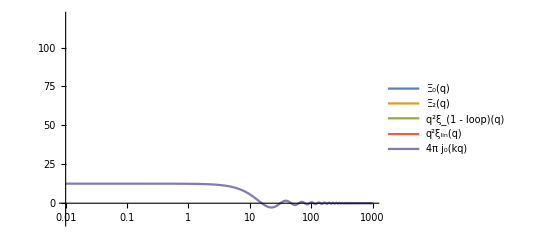

```mathematica
ktest = 0.2 ;
p1=LogLinearPlot[{   1.75Ξ0[q] ,Ξ2[q],q^2 ξE1loopFFT[q],q^2 ξ11FFT[q] ,4π SphericalBesselJ[0,ktest q] }, { q , 10^-2, 1000},PlotRange->{-12,120},PlotLegends-> {"Ξ_0(q)", "Ξ_2(q)","q^2ξ_(1 - loop)(q)", "q^2ξ_lin(q)", "4π j_0(kq)" }]
(*Export["IRcorrections.pdf",p1]*)
```

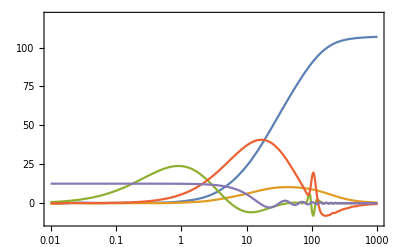

-Graphics-

```mathematica
LogLinearPlot[{   2/3(Ξ0[q]-Ξ2[q]),2 Ξ2[q], X1[1][q] ,Y1[1][q]} , { q , 10^-1, 1000},PlotRange->{-10,50},PlotStyle->{Thick, Thick, Dashed ,Dashed}]
```

Fourier::fftl: Argument {{1.×10^10 Plin[0.00001]},{1.58117×10^10 Plin[0.0000214602]},{2.50011×10^10 Plin[0.0000460539]},«14»,{3.94720170949417×10^-556 Plin[4.34274]},{1.25653760161513×10^-2606 Plin[9.31959]},{1.10919926658257×10^-12050 Plin[20.]}} is not a non-empty list or rectangular array of numeric quantities.

Part::partw: Part 11 of Fourier[{{1.×10^10 Plin[0.00001]},{1.58117×10^10 Plin[0.0000214602]},{2.50011×10^10 Plin[0.0000460539]},«14»,{3.94720170949417×10^-556 Plin[4.34274]},{1.25653760161513×10^-2606 Plin[9.31959]},{1.10919926658257×10^-12050 Plin[20.]}},FourierParameters→{-1.,-1.}] does not exist.

Fourier::fftl: Argument {{1.×10^10 Plin[0.00001]},{1.58117×10^10 Plin[0.0000214602]},{2.50011×10^10 Plin[0.0000460539]},«14»,{3.94720170949417×10^-556 Plin[4.34274]},{1.25653760161513×10^-2606 Plin[9.31959]},{1.10919926658257×10^-12050 Plin[20.]}} is not a non-empty list or rectangular array of numeric quantities.

Part::partw: Part 10 of Fourier[{{1.×10^10 Plin[0.00001]},{1.58117×10^10 Plin[0.0000214602]},{2.50011×10^10 Plin[0.0000460539]},«14»,{3.94720170949417×10^-556 Plin[4.34274]},{1.25653760161513×10^-2606 Plin[9.31959]},{1.10919926658257×10^-12050 Plin[20.]}},FourierParameters→{-1.,-1.}] does not exist.

Fourier::fftl: Argument {{1.×10^10 Plin[0.00001]},{1.58117×10^10 Plin[0.0000214602]},{2.50011×10^10 Plin[0.0000460539]},«14»,{3.94720170949417×10^-556 Plin[4.34274]},{1.25653760161513×10^-2606 Plin[9.31959]},{1.10919926658257×10^-12050 Plin[20.]}} is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier::fftl will be suppressed during this calculation.

Part::partw: Part 9 of Fourier[{{1.×10^10 Plin[0.00001]},{1.58117×10^10 Plin[0.0000214602]},{2.50011×10^10 Plin[0.0000460539]},«14»,{3.94720170949417×10^-556 Plin[4.34274]},{1.25653760161513×10^-2606 Plin[9.31959]},{1.10919926658257×10^-12050 Plin[20.]}},FourierParameters→{-1.,-1.}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

-Graphics-

### IR-correction integrands

For fast computation, I compute only a, b, c up to 4 and l, lpr = 4 (which is enough at the order n_X and n_Y that we work)

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/pierre/Documents/github/pybird

compute spherical bessel derivatives j_l^(c)(x)

```mathematica
Clear[jc]
Do[ Monitor[jc[c][l][x_] =  D[SphericalBesselJ[l,x],{x,c}]//Simplify ,{ c , l }], {c, 0,4} , {l , 0,8}]
```

compute n_j^b(l’)

```mathematica
Clear[n];
Do[ n[b][j][lpr] = Integrate[ (2(j + lpr) + 1)/2 μ^b LegendreP[j + lpr , μ ] LegendreP[lpr , μ] , { μ , -1 , 1}], { b, 0,4} , {j , -4,4} , {lpr,0,4,2}]
```

compute (I^a)_(l,l')(k,q)

```mathematica
orderTaylor = 3;
Do[ Monitor[Iint[a][l][lpr][k_,q_] = Integrate[(LegendreP[l,μk] μk^a Normal[ Series[ ⅇ^(-λ k^2/2(2+ff)ff X1 (μk^2-β)) , {λ , 0 , orderTaylor}]]LegendreP[lpr,μk]/.λ->1//FunctionExpand),{μk,-1,1}]//Simplify ,{a, l , lpr}], { a ,0,4}, {l,{0,2,4}} , {lpr,0,8}]
```

compute (L_(l,l'))^abc(k,q)

```mathematica
Clear[L];
Monitor[ Do[ L[a][b][c][l][lpr][k_,q_] = Sum[ (-ⅈ)^c(-ⅈ)^j n[b][j][lpr] *jc[c][lpr + j][k q] *Iint[a][l][lpr+j][k,q] , {j , If[ lpr-b<0,-lpr,-b],b}] , {a,0,4},{b,0,4},{c,0,4},{l,0,4,2}, {lpr ,0,4,2}], { a, b,c,l,lpr}] ;
```

compute κ_abc(L_(l,l'))^abc(k,q) (||)_0

```mathematica
fullterm1 = Coefficient[ Series[ Exp[-1/2 λ k^2 Y1( kdq^2 - α + 2 ff μk μq kdq + ff^2 μk^2 μq^2)] , {λ , 0 , 1}]//Normal , λ^1]//Expand;
fullterm2 = Coefficient[ Series[ Exp[-1/2 λ k^2 Y1 ( kdq^2 - α + 2 ff μk μq kdq + ff^2 μk^2 μq^2)] , {λ , 0 , 2}]//Normal , λ^2]//Expand;
Clear[K1,K2]
K1[l_][lpr_][k_,q_] =  Sum[ Coefficient[ μk μq kdq fullterm1 , μk^a μq^b kdq^c]L[a-1][b-1][c-1][l][lpr][k,q] , { a , 1 , 7}, { b , 1 , 7}, { c , 1, 7}];
K2[l_][lpr_][k_,q_] = Sum[ Coefficient[ μk μq kdq fullterm2 , μk^a μq^b kdq^c]L[a-1][b-1][c-1][l][lpr][k,q] , { a , 1 , 7}, { b , 1 , 7}, { c , 1, 7}];
```

Q_0 for IR-resummation

```mathematica
Q0[k_,q_,l_,lpr_]=    (2l+1)/2 ⅇ^(-k^2/2(X1+Y1 α))   ⅇ^(-k^2/2(2+ff)ff X1 β)(L[0][0][0][l][lpr][k,q]+K1[l][lpr][k,q] +0K2[l][lpr][k,q] )  ;
```

Q_1 for IR-resummation

```mathematica
yorder =1;
exps = Exp[-1/2 λ1 k^2 Y1 ( kdq^2 - α + 2 ff μk μq kdq + ff^2 μk^2 μq^2)]Exp[ λ2 k^2/2( X1(1 + μk^2 ff(2+ff))  + Y1 ( kdq^2 + 2 μk μq ff kdq + ff^2 μk^2 μq^2))] ;
expand=(Series[ Series[ Series[ exps , { λ1 , 0 , yorder}]//Normal , {λ2, 0 ,1}]//Normal , { Y1 , 0 , yorder}]//Normal )/. {λ1->1 , λ2->1} ;
(*exps = Exp[-1/2 k^2 Y1 ( kdq^2 - α + 2 ff μk μq kdq + ff^2 μk^2 μq^2)]Exp[ λ2 k^2/2( X1(1 + μk^2 ff(2+ff))  + Y1 ( kdq^2 + 2 μk μq ff kdq + ff^2 μk^2 μq^2))] ;
expand=(Series[ Series[  exps , {λ2, 0 ,1}]//Normal , { Y1 , 0 , yorder}]//Normal )/. {λ1->1 , λ2->1} ;*)
J[l_][lpr_][k_,q_] = Sum[ Coefficient[ μk μq kdq expand , μk^a μq^b kdq^c]L[a-1][b-1][c-1][l][lpr][k,q] , { a , 1 , 7}, { b , 1 , 7}, { c , 1, 7}] ;
Q1[k_,q_,l_,lpr_]= (2l + 1)/2 ⅇ^(-k^2/2( X1 + α Y1)) ⅇ^(-k^2/2(2+ff)ff X1 β)J[l][lpr][k,q] ;
```

```mathematica
(*Q1tab =Table[Coefficient[Series[k Q1[k, q, l,lp]/(ⅇ^(-k^2/2( X1 + α Y1)) ⅇ^(-k^2/2(2+ff)ff X1 β))/.rep//Simplify,{k,0,10}]//Normal,{k, k^2,k^3,k^4,k^5,k^6,k^7,k^8,k^9,k^10}]//Simplify,{l,{0,2,4}},{lp,{0,2,4}}];
MatrixForm[Q1tab]
kpowlist1 = {1,k,k^2,k^3,k^4,k^5,k^7,k^8,k^9};
(*Verification*)
Table[(Q1tab⟦l/2+1,lp/2+1⟧.kpowlist1 ⅇ^(-1/3 k^2(Ξ0+1/3 ff(2+ff)(Ξ0-Ξ2)))SphericalBesselJ[lp, k q]-Q1[k, q, l,lp]/.rep)//Simplify,{l,{0,2,4}},{lp,{0,2,4}}]*)
```

```mathematica
SBrep5={SphericalBesselJ[5,x_]->9/x SphericalBesselJ[4,x]-SphericalBesselJ[3,x]};
SBrep3={SphericalBesselJ[3,x_]-> 5/x SphericalBesselJ[2,x]-SphericalBesselJ[1,x] };
SBrep1={SphericalBesselJ[1,x_]-> x/3(SphericalBesselJ[0,x]+SphericalBesselJ[2,x])};
Fakerep={SphericalBesselJ[0,x_ ]-> j0,SphericalBesselJ[2,x_ ]-> j2,  SphericalBesselJ[4,x_ ]-> j4,SphericalBesselJ[6,x_ ]-> j6};
ab={α-> 0,β-> 0};
```

```mathematica
Xp = {k^3 X1,k^5 X1^2,k^7 X1^3,k^9 X1^4};
YXp={k^3 Y1,k^5 Y1 X1,k^7 Y1 X1^2,k^9 Y1 X1^3};
jlist02 = {j0, j2};
jlist024={j0,j2,j4};
jklist = {j0 k,j2 k,j4 k} ;
j2k2YXp={j2  k^3 X1 Y1,j2 k^5 X1^2 Y1,j2 k^7 X1^3 Y1,j2 k^9 X1^4 Y1};
j2k2YXpqm2={q^-2 j2  k^3 X1 Y1,q^-2 j2 k^5 X1^2 Y1,q^-2 j2 k^7 X1^3 Y1,q^-2 j2 k^9 X1^4 Y1};
megalist=Join[jklist,Outer[Times,Xp,  jlist02],Outer[Times,YXp,jlist024],j2k2YXp,{j2 k Y1}]//Flatten
megalistq=Join[jklist,Outer[Times,Xp,  jlist02],Outer[Times,YXp,jlist024],j2k2YXpqm2,{q^-2 j2 k Y1}]//Flatten
Length[megalistq]
```

{j0 k,j2 k,j4 k,j0 k^3 X1,j2 k^3 X1,j0 k^5 X1^2,j2 k^5 X1^2,j0 k^7 X1^3,j2 k^7 X1^3,j0 k^9 X1^4,j2 k^9 X1^4,j0 k^3 Y1,j2 k^3 Y1,j4 k^3 Y1,j0 k^5 X1 Y1,j2 k^5 X1 Y1,j4 k^5 X1 Y1,j0 k^7 X1^2 Y1,j2 k^7 X1^2 Y1,j4 k^7 X1^2 Y1,j0 k^9 X1^3 Y1,j2 k^9 X1^3 Y1,j4 k^9 X1^3 Y1,j2 k^3 X1 Y1,j2 k^5 X1^2 Y1,j2 k^7 X1^3 Y1,j2 k^9 X1^4 Y1,j2 k Y1}

{j0 k,j2 k,j4 k,j0 k^3 X1,j2 k^3 X1,j0 k^5 X1^2,j2 k^5 X1^2,j0 k^7 X1^3,j2 k^7 X1^3,j0 k^9 X1^4,j2 k^9 X1^4,j0 k^3 Y1,j2 k^3 Y1,j4 k^3 Y1,j0 k^5 X1 Y1,j2 k^5 X1 Y1,j4 k^5 X1 Y1,j0 k^7 X1^2 Y1,j2 k^7 X1^2 Y1,j4 k^7 X1^2 Y1,j0 k^9 X1^3 Y1,j2 k^9 X1^3 Y1,j4 k^9 X1^3 Y1,(j2 k^3 X1 Y1)/q^2,(j2 k^5 X1^2 Y1)/q^2,(j2 k^7 X1^3 Y1)/q^2,(j2 k^9 X1^4 Y1)/q^2,(j2 k Y1)/q^2}

28

```mathematica
(*megalist ={j0 k,j2 k,j4 k, j0 k^3 X1,j0 k^5 X1^2,j0 k^7 X1^3,j0 k^9 X1^4, j2 k^3 X1,j2 k^5 X1^2,j2 k^7 X1^3,j2 k^9 X1^4,
(*j4 k^3 X1, j4 k^5 X1^2,j4 k^7 X1^3,j4 k^9 X1^4,*)
 (*j6 k^3 X1,j6 k^5 X1^2,j6 k^7 X1^3,j6 k^9 X1^4,*)
j0 k^3 Y1,j0 k^5 X1 Y1,j0 k^7 X1^2 Y1,j0 k^9 X1^3 Y1, j2 k^3 Y1,j2 k^5 X1 Y1,j2 k^7 X1^2 Y1,j2 k^9 X1^3 Y1,j4 k^3 Y1,j4 k^5 X1 Y1,j4 k^7 X1^2 Y1,j4 k^9 X1^3 Y1,
(*j6 k^3 Y1,j6 k^5 X1 Y1,j6 k^7 X1^2 Y1,j6 k^9 X1^3 Y1,*)
j2  k^3 X1 Y1,j2 k^5 X1^2 Y1,j2 k^7 X1^3 Y1,j2 k^9 X1^4 Y1,
j2 k Y1} ;
megalistq ={j0 k,j2 k,j4 k, j0 k^3 X1,j0 k^5 X1^2,j0 k^7 X1^3,j0 k^9 X1^4, j2 k^3 X1,j2 k^5 X1^2,j2 k^7 X1^3,j2 k^9 X1^4,
(*j4 k^3 X1,j4 k^5 X1^2,j4 k^7 X1^3,j4 k^9 X1^4,*)
(*j6 k^3 X1,j6 k^5 X1^2,j6 k^7 X1^3,j6 k^9 X1^4,*)
j0 k^3 Y1,j0 k^5 X1 Y1,j0 k^7 X1^2 Y1,j0 k^9 X1^3 Y1, j2 k^3 Y1,j2 k^5 X1 Y1,j2 k^7 X1^2 Y1,j2 k^9 X1^3 Y1,j4 k^3 Y1,j4 k^5 X1 Y1,j4 k^7 X1^2 Y1,j4 k^9 X1^3 Y1,
(*j6 k^3 Y1,j6 k^5 X1 Y1,j6 k^7 X1^2 Y1,j6 k^9 X1^3 Y1,*)
j2 q^-2  k^3 X1 Y1,j2 q^-2 k^5 X1^2 Y1,j2 q^-2 k^7 X1^3 Y1,j2 q^-2 k^9 X1^4 Y1,
j2 q^-2 k Y1} ;*)

(*coefQ1=Table[Coefficient[Series[k (Q1[k, q, l,lp]/.SBrep3/.SBrep1)/(ⅇ^(-k^2/2( X1 + α Y1)) ⅇ^(-k^2/2(2+ff)ff X1 β))/.Fakerep/.{β-> 1/3, α-> 1/3},{k,0,9}]//Normal,megalist]/.{X1-> 0,Y1-> 0}//Simplify,{l,{0,2}},{lp,{0,2}}] ;*)
(*Table[(coefQ1⟦l/2+1,lp/2+1⟧.megalist- Series[k (Q1[k, q, l,lp]/.SBrep3/.SBrep1)/(ⅇ^(-k^2/2( X1 + α Y1)) ⅇ^(-k^2/2(2+ff)ff X1 β))/.Fakerep/.{β-> 1/3, α-> 1/3},{k,0,9}]//Normal)//Simplify,{l,{0,2}},{lp,{0,2}}]*)
coefQ1=Table[Coefficient[Series[k Q1[k, q, l,lp]/.SBrep3/.SBrep1/.Fakerep/.ab,{k,0,9}]//Normal,megalist]/.{X1-> 0,Y1-> 0,q-> 1}//Simplify,{l,{0,2}},{lp,{0,2}}] ;
Table[(coefQ1⟦l/2+1,lp/2+1⟧.megalistq- Series[k Q1[k, q, l,lp]/.SBrep3/.SBrep1 /.Fakerep/.ab,{k,0,9}]//Normal)//Simplify,{l,{0,2}},{lp,{0,2}}]
coefQ1//MatrixForm
```

{{0,0},{0,0}}

((1
0
0
0
0
1/120 (-15-20 ff-22 ff^2-12 ff^3-3 ff^4)
0
1/840 (35+70 ff+119 ff^2+124 ff^3+81 ff^4+30 ff^5+5 ff^6)
0
(-945-2520 ff-5796 ff^2-8856 ff^3-9854 ff^4-7720 ff^5-3900 ff^6-1120 ff^7-140 ff^8)/120960
0
0
0
0
1/180 (-15+2 ff^2-3 ff^4)
1/630 (105-35 ff^2-18 ff^3+12 ff^4)
0
(105+70 ff+21 ff^2-36 ff^3+3 ff^4+30 ff^5+15 ff^6)/2520
(-105-70 ff+72 ff^3+35 ff^4-10 ff^5-10 ff^6)/1260
0
(-315-420 ff-420 ff^2-36 ff^3+182 ff^4+20 ff^5-180 ff^6-140 ff^7-35 ff^8)/30240
(3465+4620 ff+3927 ff^2-1386 ff^3-4873 ff^4-3040 ff^5+225 ff^6+910 ff^7+280 ff^8)/166320
0
0
0
0
0
0) | (0
0
0
0
0
0
-1/210 ff (14+19 ff+12 ff^2+3 ff^3)
0
(ff (42+93 ff+112 ff^2+78 ff^3+30 ff^4+5 ff^5))/1260
0
-(ff (1386+4257 ff+7524 ff^2+9071 ff^3+7450 ff^4+3855 ff^5+1120 ff^6+140 ff^7))/166320
0
0
0
(ff (-350-159 ff+36 ff^2+84 ff^3))/12600
(ff (-98+273 ff+72 ff^2-132 ff^3))/8820
(ff (490-259 ff-124 ff^2+64 ff^3))/29400
(ff (210+289 ff+184 ff^2-29 ff^3-80 ff^4-30 ff^5))/12600
(ff (294+70 ff-212 ff^2-103 ff^3+80 ff^4+55 ff^5))/8820
-(ff (5390+1771 ff-2904 ff^2-2381 ff^3+380 ff^4+480 ff^5))/323400
(ff (-16170-36861 ff-46596 ff^2-27034 ff^3+1370 ff^4+12675 ff^5+7420 ff^6+1540 ff^7))/3326400
-(ff (35574+45969 ff+11352 ff^2-26882 ff^3-18950 ff^4+6585 ff^5+10640 ff^6+3080 ff^7))/2328480
(ff (210210+249249 ff+26884 ff^2-218634 ff^3-171330 ff^4-5575 ff^5+42420 ff^6+13440 ff^7))/33633600
1/840 ff (182+19 ff-36 ff^2)
1/840 ff (-182-175 ff-40 ff^2+41 ff^3+20 ff^4)
(ff (6006+10923 ff+9548 ff^2+2514 ff^3-2070 ff^4-1805 ff^5-420 ff^6))/73920
(ff (-78078-208923 ff-305448 ff^2-245453 ff^3-73810 ff^4+49395 ff^5+59780 ff^6+24325 ff^7+3780 ff^8))/4324320
0)
(0
0
0
0
0
-1/42 ff (14+19 ff+12 ff^2+3 ff^3)
0
1/252 ff (42+93 ff+112 ff^2+78 ff^3+30 ff^4+5 ff^5)
0
-(ff (1386+4257 ff+7524 ff^2+9071 ff^3+7450 ff^4+3855 ff^5+1120 ff^6+140 ff^7))/33264
0
0
0
0
1/63 (5 ff^2-3 ff^4)
1/126 ff^2 (-23-6 ff+9 ff^2)
0
1/252 ff (14-3 ff-16 ff^2-2 ff^3+10 ff^4+5 ff^5)
(ff (-308+99 ff+484 ff^2+210 ff^3-120 ff^4-85 ff^5))/2772
0
-(ff (231+231 ff-66 ff^2-263 ff^3-65 ff^4+165 ff^5+140 ff^6+35 ff^7))/8316
(ff (24024+22737 ff-14586 ff^2-42913 ff^3-24340 ff^4+5415 ff^5+10150 ff^6+2905 ff^7))/432432
0
0
0
0
0
0) | (0
1
0
0
0
0
1/168 (-21-44 ff-58 ff^2-36 ff^3-9 ff^4)
0
(231+726 ff+1551 ff^2+1868 ff^3+1317 ff^4+510 ff^5+85 ff^6)/5544
0
(-27027-113256 ff-334620 ff^2-596232 ff^3-732778 ff^4-610520 ff^5-318660 ff^6-92960 ff^7-11620 ff^8)/3459456
0
0
0
(-105-226 ff-159 ff^2+84 ff^3+96 ff^4)/5040
(-735-154 ff+381 ff^2+108 ff^3-198 ff^4)/3528
(8085+154 ff-6589 ff^2-2116 ff^3+2176 ff^4)/129360
(1155+3696 ff+6710 ff^2+3892 ff^3-1377 ff^4-2580 ff^5-880 ff^6)/110880
(8085+10164 ff+2816 ff^2-7556 ff^3-3739 ff^4+2720 ff^5+1870 ff^6)/77616
(-105105-112112 ff+18590 ff^2+173316 ff^3+85499 ff^4-36740 ff^5-27840 ff^6)/3363360
(-45045-191334 ff-532389 ff^2-696072 ff^3-395423 ff^4+84250 ff^5+260265 ff^6+145460 ff^7+29120 ff^8)/17297280
(-315315-726726 ff-923637 ff^2-183144 ff^3+601429 ff^4+426490 ff^5-125655 ff^6-220780 ff^7-63910 ff^8)/12108096
(105105+222222 ff+228657 ff^2-128024 ff^3-418221 ff^4-254130 ff^5+39035 ff^6+93660 ff^7+26880 ff^8)/13453440
1/336 (273+178 ff-25 ff^2-84 ff^3)
(-3003-5104 ff-4598 ff^2-20 ff^3+1993 ff^4+820 ff^5)/7392
(39039+107250 ff+190047 ff^2+151736 ff^3+17373 ff^4-61710 ff^5-43595 ff^6-9660 ff^7)/384384
(-117117-444444 ff-1161732 ff^2-1672008 ff^3-1279078 ff^4-236480 ff^5+463500 ff^6+448840 ff^7+173915 ff^8+26460 ff^9)/6918912
0))

```mathematica
Export["../../cbirdy/Q1.txt",Table[FortranForm[coefQ1⟦2,1,i⟧],{i,4,Length[coefQ1⟦1,1⟧]}], "Table"];
```

```mathematica
coefQ0=Table[Coefficient[Series[k Q0[k, q, l,lp]/.SBrep3/.SBrep1/.Fakerep/.ab,{k,0,9}]//Normal,megalist]/.{X1-> 0,Y1-> 0}/.{q-> 1}//Simplify,{l,{0,2}},{lp,{0,2}}] ;
Table[(coefQ0⟦l/2+1,lp/2+1⟧.megalistq- Series[k Q0[k, q, l,lp]/.SBrep3/.SBrep1 /.Fakerep/.ab,{k,0,9}]//Normal)//Simplify,{l,{0,2}},{lp,{0,2}}]
coefQ0//MatrixForm
```

{{0,0},{0,0}}

((1
0
0
1/6 (-3-2 ff-ff^2)
0
1/120 (15+20 ff+22 ff^2+12 ff^3+3 ff^4)
0
(-35-70 ff-119 ff^2-124 ff^3-81 ff^4-30 ff^5-5 ff^6)/1680
0
(105+280 ff+644 ff^2+984 ff^3+846 ff^4+360 ff^5+60 ff^6)/40320
0
1/18 (-3+2 ff-ff^2)
1/45 (15-10 ff+2 ff^2)
0
1/180 (15-2 ff^2+3 ff^4)
1/630 (-105+35 ff^2+18 ff^3-12 ff^4)
0
(-105-70 ff-21 ff^2+36 ff^3-3 ff^4-30 ff^5-15 ff^6)/5040
(105+70 ff-72 ff^3-35 ff^4+10 ff^5+10 ff^6)/2520
0
(315+420 ff+420 ff^2+36 ff^3-182 ff^4-20 ff^5+180 ff^6+140 ff^7+35 ff^8)/90720
(-3465-4620 ff-3927 ff^2+1386 ff^3+4873 ff^4+3040 ff^5-225 ff^6-910 ff^7-280 ff^8)/498960
0
0
0
0
0
0) | (0
0
0
0
-1/15 ff (2+ff)
0
1/210 ff (14+19 ff+12 ff^2+3 ff^3)
0
-(ff (42+93 ff+112 ff^2+78 ff^3+30 ff^4+5 ff^5))/2520
0
(ff (14+43 ff+76 ff^2+69 ff^3+30 ff^4+5 ff^5))/5040
1/45 (-2+ff) ff
1/315 (28-11 ff) ff
0
(ff (350+159 ff-36 ff^2-84 ff^3))/12600
(ff (98-273 ff-72 ff^2+132 ff^3))/8820
(ff (-490+259 ff+124 ff^2-64 ff^3))/29400
(ff (-210-289 ff-184 ff^2+29 ff^3+80 ff^4+30 ff^5))/25200
-(ff (294+70 ff-212 ff^2-103 ff^3+80 ff^4+55 ff^5))/17640
(ff (5390+1771 ff-2904 ff^2-2381 ff^3+380 ff^4+480 ff^5))/646800
(ff (16170+36861 ff+46596 ff^2+27034 ff^3-1370 ff^4-12675 ff^5-7420 ff^6-1540 ff^7))/9979200
(ff (35574+45969 ff+11352 ff^2-26882 ff^3-18950 ff^4+6585 ff^5+10640 ff^6+3080 ff^7))/6985440
-(ff (210210+249249 ff+26884 ff^2-218634 ff^3-171330 ff^4-5575 ff^5+42420 ff^6+13440 ff^7))/100900800
1/840 ff (-182-19 ff+36 ff^2)
(ff (182+175 ff+40 ff^2-41 ff^3-20 ff^4))/1680
(ff (-6006-10923 ff-9548 ff^2-2514 ff^3+2070 ff^4+1805 ff^5+420 ff^6))/221760
(ff (2002+5357 ff+7832 ff^2+3867 ff^3-1410 ff^4-1805 ff^5-420 ff^6))/443520
0)
(0
0
0
-1/3 ff (2+ff)
0
1/42 ff (14+19 ff+12 ff^2+3 ff^3)
0
-1/504 ff (42+93 ff+112 ff^2+78 ff^3+30 ff^4+5 ff^5)
0
(ff (14+43 ff+76 ff^2+69 ff^3+30 ff^4+5 ff^5))/1008
0
-1/9 (-2+ff) ff
1/63 ff (-28+11 ff)
0
1/63 ff^2 (-5+3 ff^2)
1/126 ff^2 (23+6 ff-9 ff^2)
0
1/504 ff (-14+3 ff+16 ff^2+2 ff^3-10 ff^4-5 ff^5)
(ff (308-99 ff-484 ff^2-210 ff^3+120 ff^4+85 ff^5))/5544
0
(ff (231+231 ff-66 ff^2-263 ff^3-65 ff^4+165 ff^5+140 ff^6+35 ff^7))/24948
-(ff (24024+22737 ff-14586 ff^2-42913 ff^3-24340 ff^4+5415 ff^5+10150 ff^6+2905 ff^7))/1297296
0
0
0
0
0
0) | (0
1
0
0
1/42 (-21-22 ff-11 ff^2)
0
1/168 (21+44 ff+58 ff^2+36 ff^3+9 ff^4)
0
(-231-726 ff-1551 ff^2-1868 ff^3-1317 ff^4-510 ff^5-85 ff^6)/11088
0
(231+968 ff+2860 ff^2+5096 ff^3+4674 ff^4+2040 ff^5+340 ff^6)/88704
-1/24-(29 ff)/630+(2 ff^2)/45
(-735+616 ff-242 ff^2)/1764
1/8-(9 ff)/70+(8 ff^2)/245
(105+226 ff+159 ff^2-84 ff^3-96 ff^4)/5040
(735+154 ff-381 ff^2-108 ff^3+198 ff^4)/3528
(-8085-154 ff+6589 ff^2+2116 ff^3-2176 ff^4)/129360
(-1155-3696 ff-6710 ff^2-3892 ff^3+1377 ff^4+2580 ff^5+880 ff^6)/221760
(-8085-10164 ff-2816 ff^2+7556 ff^3+3739 ff^4-2720 ff^5-1870 ff^6)/155232
(105105+112112 ff-18590 ff^2-173316 ff^3-85499 ff^4+36740 ff^5+27840 ff^6)/6726720
(45045+191334 ff+532389 ff^2+696072 ff^3+395423 ff^4-84250 ff^5-260265 ff^6-145460 ff^7-29120 ff^8)/51891840
(315315+726726 ff+923637 ff^2+183144 ff^3-601429 ff^4-426490 ff^5+125655 ff^6+220780 ff^7+63910 ff^8)/36324288
(-105105-222222 ff-228657 ff^2+128024 ff^3+418221 ff^4+254130 ff^5-39035 ff^6-93660 ff^7-26880 ff^8)/40360320
1/336 (-273-178 ff+25 ff^2+84 ff^3)
(3003+5104 ff+4598 ff^2+20 ff^3-1993 ff^4-820 ff^5)/14784
(-39039-107250 ff-190047 ff^2-151736 ff^3-17373 ff^4+61710 ff^5+43595 ff^6+9660 ff^7)/1153152
(39039+148148 ff+387244 ff^2+557336 ff^3+224946 ff^4-182880 ff^5-174380 ff^6-38640 ff^7)/9225216
13/8-(9 ff)/14))

```mathematica
Export["../../cbirdy/Q1.txt",Table[FortranForm[coefQ0⟦2,1,i⟧],{i,4,Length[coefQ1⟦1,1⟧]}], "Table"];
```

```mathematica
Q1[k, q, 4,4]/.SBrep3/.SBrep1/.Fakerep/.ab
```

9/2 ⅇ^(-(k^2 X1)/2-1/6 ff (2+ff) k^2 X1) (1/24504480 j4 (4 ff k^2 X1+2 ff^2 k^2 X1) (689520-294848 ff k^2 X1-115648/9 ff^5 k^6 X1^3-57824/27 ff^6 k^6 X1^3+6 ff^4 k^4 X1^2 (32164/9-(115648 k^2 X1)/27)+8 ff^3 k^4 X1^2 (32164/3-(57824 k^2 X1)/27)+408 ff^2 k^2 X1 (-1084/3+(1892 k^2 X1)/9))+j4 (1+(k^2 X1)/2) (2/9+(ff (2+ff) k^2 X1 (-20800+ff (2+ff) k^2 X1 (11574-39140/27 ff (2+ff) k^2 X1-65/3 (-154+39 ff (2+ff) k^2 X1)+3 (-3380+643 ff (2+ff) k^2 X1))))/1081080)+1/(49008960 q^2)k^2 (4 ff X1+2 ff^2 X1) (689520-294848 ff k^2 X1-115648/9 ff^5 k^6 X1^3-57824/27 ff^6 k^6 X1^3+6 ff^4 k^4 X1^2 (32164/9-(115648 k^2 X1)/27)+8 ff^3 k^4 X1^2 (32164/3-(57824 k^2 X1)/27)+408 ff^2 k^2 X1 (-1084/3+(1892 k^2 X1)/9)) Y1 (-j4 (-12+k^2 q^2)+2 k q SphericalBesselJ[5,k q])+(k^2 X1 (2/9+(ff (2+ff) k^2 X1 (-20800+ff (2+ff) k^2 X1 (11574-39140/27 ff (2+ff) k^2 X1-65/3 (-154+39 ff (2+ff) k^2 X1)+3 (-3380+643 ff (2+ff) k^2 X1))))/1081080) Y1 (-j4 (-12+k^2 q^2)+2 k q SphericalBesselJ[5,k q]))/(4 q^2)-1/4 ff^2 k^4 X1 Y1 (-(2 j2 (6864-4784 ff k^2 X1-2096/9 ff^5 k^6 X1^3-1048/27 ff^6 k^6 X1^3+2 ff^4 k^4 X1^2 (188-(2096 k^2 X1)/9)+8 ff^3 k^4 X1^2 (188-(1048 k^2 X1)/27)+8 ff^2 k^2 X1 (-299+188 k^2 X1)))/945945+(j4 (689520-294848 ff k^2 X1-115648/9 ff^5 k^6 X1^3-57824/27 ff^6 k^6 X1^3+6 ff^4 k^4 X1^2 (32164/9-(115648 k^2 X1)/27)+8 ff^3 k^4 X1^2 (32164/3-(57824 k^2 X1)/27)+408 ff^2 k^2 X1 (-1084/3+(1892 k^2 X1)/9)))/12095160-1/192053862(2713200-1834640 ff k^2 X1-751496/9 ff^5 k^6 X1^3-375748/27 ff^6 k^6 X1^3+2 ff^4 k^4 X1^2 (66880-(751496 k^2 X1)/9)+8 ff^3 k^4 X1^2 (66880-(375748 k^2 X1)/27)+760 ff^2 k^2 X1 (-1207+704 k^2 X1)) SphericalBesselJ[6,k q])-1/8 ff^2 k^4 (4 ff X1+2 ff^2 X1) Y1 (-(2 j2 (360672-234736 ff k^2 X1-101072/9 ff^5 k^6 X1^3-50536/27 ff^6 k^6 X1^3+12 ff^4 k^4 X1^2 (13702/9-(50536 k^2 X1)/27)+8 ff^3 k^4 X1^2 (27404/3-(50536 k^2 X1)/27)+408 ff^2 k^2 X1 (-863/3+(1612 k^2 X1)/9)))/48243195+1/229808040 j4 (9969072+ff (2+ff) k^2 X1 (-2563328+ff (2+ff) k^2 X1 (207689/27 ff (2+ff) k^2 X1+315 (3002-461 ff (2+ff) k^2 X1)-323/3 (-1286+545 ff (2+ff) k^2 X1)+95 (-7412+1659 ff (2+ff) k^2 X1))))-1/576161586(8217120-5044880 ff k^2 X1-2171752/9 ff^5 k^6 X1^3-1085876/27 ff^6 k^6 X1^3+12 ff^4 k^4 X1^2 (288194/9-(1085876 k^2 X1)/27)+8 ff^3 k^4 X1^2 (576388/3-(1085876 k^2 X1)/27)+24 ff^2 k^2 X1 (-315305/3+(576388 k^2 X1)/9)) SphericalBesselJ[6,k q])-1/2 ff k^4 X1 Y1 (((j2-((5 j2)/(k q)-1/3 (j0+j2) k q+j4 k q)/(k q)) (34320-14768 ff k^2 X1-5968/9 ff^5 k^6 X1^3-2984/27 ff^6 k^6 X1^3+6 ff^4 k^4 X1^2 (1624/9-(5968 k^2 X1)/27)+8 ff^3 k^4 X1^2 (1624/3-(2984 k^2 X1)/27)+24 ff^2 k^2 X1 (-923/3+(1624 k^2 X1)/9)))/1216215-1/66162096 5 (371280-157760 ff k^2 X1-59968/9 ff^5 k^6 X1^3-29984/27 ff^6 k^6 X1^3+6 ff^4 k^4 X1^2 (17068/9-(59968 k^2 X1)/27)+8 ff^3 k^4 X1^2 (17068/3-(29984 k^2 X1)/27)+408 ff^2 k^2 X1 (-580/3+(1004 k^2 X1)/9)) (j4-(SphericalBesselJ[5,k q]+k q SphericalBesselJ[6,k q])/(k q)))-1/4 ff k^4 (4 ff X1+2 ff^2 X1) Y1 (1/6891885(j2-((5 j2)/(k q)-1/3 (j0+j2) k q+j4 k q)/(k q)) (148512-76976 ff k^2 X1-31792/9 ff^5 k^6 X1^3-15896/27 ff^6 k^6 X1^3+12 ff^4 k^4 X1^2 (4352/9-(15896 k^2 X1)/27)+8 ff^3 k^4 X1^2 (8704/3-(15896 k^2 X1)/27)+408 ff^2 k^2 X1 (-283/3+(512 k^2 X1)/9))-1/419026608(8914800-4547840 ff k^2 X1-1818592/9 ff^5 k^6 X1^3-909296/27 ff^6 k^6 X1^3+6 ff^4 k^4 X1^2 (496660/9-(1818592 k^2 X1)/27)+8 ff^3 k^4 X1^2 (496660/3-(909296 k^2 X1)/27)+2280 ff^2 k^2 X1 (-2992/3+(5228 k^2 X1)/9)) (j4-(SphericalBesselJ[5,k q]+k q SphericalBesselJ[6,k q])/(k q))))

```mathematica
Q1tab =Coefficient[Series[k Coefficient[Q1[k, q, 0,0]/(ⅇ^(-k^2/2( X1 + α Y1)) ⅇ^(-k^2/2(2+ff)ff X1 β))/.rep/.SBrep,{SphericalBesselJ[0,k q],SphericalBesselJ[2,k q]}],{k,0,5}]//Normal,{k, k^2,k^3,k^4,k^5}];
MatrixForm[Q1tab]
kpowlist1 = {1,k,k^2,k^3,k^4};
(*Verification*)
(*Table[(Q1tab⟦l/2+1,lp/2+1⟧.kpowlist1 ⅇ^(-1/3 k^2(Ξ0+1/3 ff(2+ff)(Ξ0-Ξ2)))-Q1[k, q, l,lp]/.rep)//Simplify,{l,{0,2}},{lp,{0,2}}]*)
```

ReplaceAll::reps: {rep} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Thread::tdlen: Objects of unequal length in Coefficient[{0,0},{k,k^2,k^3,k^4,k^5}] cannot be combined.

{}

Final integrand written in a synthetic way: 4π q^2 ξ_j^l'(q) Q_(N-j,ll')(k q) = 4πq^2 ξ_j^l'(q)  j_l'(k q) ⅇ^(-1/3 k^2(Ξ0+1/3 f(2+f)(Ξ0-Ξ2)))(k^(2p)(Ξ0-Ξ2))^p R_(N-j,ll')(p,f)
4π q^2 ξ_1^l'(q) Q_(0,ll')(k q) = 4πq^2 ξ_1^l'(q)  j_l'(k q) ⅇ^(-1/3 k^2(Ξ0+1/3 f(2+f)(Ξ0-Ξ2)))(k^(2p)(f(2+f)(Ξ0-Ξ2)))^p R_(0,ll')(p)
4π q^2 ξ_0^l'(q) Q_(1,ll')(k q) = 4πq^2 ξ_0^l'(q)  j_l'(k q) ⅇ^(-1/3 k^2(Ξ0+1/3 f(2+f)(Ξ0-Ξ2)))(k^(2p)(Ξ0-Ξ2))^p R_(1,ll')(p,f)

```mathematica
rep={α-> 1/3, β-> 1/3, X1->2/3(Ξ0-Ξ2),Y1-> 2Ξ2 } ;
```

```mathematica
Q0tab =Table[Coefficient[Series[k Q0[k, q, l,lp]/(ⅇ^(-k^2/2( X1 + α Y1)) ⅇ^(-k^2/2(2+ff)ff X1 β) SphericalBesselJ[lp, k q])/.rep//Simplify,{k,0,10}]//Normal,{k, k^3,k^5,k^7}],{l,{0,2,4}},{lp,{0,2,4}}];
 Q0tab⟦All,All,2⟧=Q0tab⟦All,All,2⟧/(ff(2+ff)(Ξ0-Ξ2))//Simplify;
 Q0tab⟦All,All,3⟧=Q0tab⟦All,All,3⟧/(ff(2+ff)(Ξ0-Ξ2))^2//Simplify;
 Q0tab⟦All,All,4⟧=Q0tab⟦All,All,4⟧/(ff(2+ff)(Ξ0-Ξ2))^3//Simplify;
MatrixForm[Q0tab]
kpowlist0 = {1,(ff(2+ff)(Ξ0-Ξ2))k^2,(ff(2+ff)(Ξ0-Ξ2))^2 k^4,(ff(2+ff)(Ξ0-Ξ2))^3 k^6};
(*Verification*)
Table[(Q0tab⟦l/2+1,lp/2+1⟧.kpowlist0 ⅇ^(-1/3 k^2(Ξ0+1/3 ff(2+ff)(Ξ0-Ξ2)))SphericalBesselJ[lp, k q]-Q0[k, q, l,lp]/.rep)//Simplify,{l,{0,2,4}},{lp,{0,2,4}}]
```

((1
0
2/405
-8/76545) | (0
-2/45
4/2835
-4/25515) | (0
0
4/2835
-16/280665)
(0
-2/9
4/567
-4/5103) | (1
-4/63
2/189
-80/168399) | (0
-4/63
8/2079
-272/729729)
(0
0
4/315
-16/31185) | (0
-4/35
8/1155
-272/405405) | (1
-40/693
3578/405405
-4936/10945935))

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Q1tab =Table[Coefficient[Series[k Q1[k, q, l,lp]/(ⅇ^(-k^2/2( X1 + α Y1)) ⅇ^(-k^2/2(2+ff)ff X1 β) SphericalBesselJ[lp, k q])/.rep//Simplify,{k,0,10}]//Normal,{k, k^3,k^5,k^7,k^9}],{l,{0,2,4}},{lp,{0,2,4}}];
 Q1tab⟦All,All,2⟧=Q1tab⟦All,All,2⟧/(Ξ0-Ξ2)//Simplify ;
 Q1tab⟦All,All,3⟧=Q1tab⟦All,All,3⟧/(Ξ0-Ξ2)^2//Simplify ;
 Q1tab⟦All,All,4⟧=Q1tab⟦All,All,4⟧/(Ξ0-Ξ2)^3//Simplify ;
Q1tab⟦All,All,5⟧=Q1tab⟦All,All,5⟧/(Ξ0-Ξ2)^4//Simplify ;
MatrixForm[Q1tab]
kpowlist1 = {1,((Ξ0-Ξ2))k^2,((Ξ0-Ξ2))^2 k^4,((Ξ0-Ξ2))^3 k^6,((Ξ0-Ξ2))^4 k^8};
(*Verification*)
Table[(Q1tab⟦l/2+1,lp/2+1⟧.kpowlist1 ⅇ^(-1/3 k^2(Ξ0+1/3 ff(2+ff)(Ξ0-Ξ2)))SphericalBesselJ[lp, k q]-Q1[k, q, l,lp]/.rep)//Simplify,{l,{0,2,4}},{lp,{0,2,4}}]
```

$Aborted

{}

Part::partw: Part 1 of {} does not exist.

$Aborted

Now expanding the exponential: up to k^6 in Q0 for the loop and up to k^8 in Q1 for the linear

```mathematica
T0[k_,q_,l_,lpr_]=    (2l+1)/2 ⅇ^(-1/3 k^2(Ξ0+1/3 ff(2+ff)(Ξ0-Ξ2)))(L[0][0][0][l][lpr][k,q])/SphericalBesselJ[lpr, k q]//Simplify;
```

```mathematica
T0tab=Table[Simplify[Coefficient[Normal[Series[k T0[k,q,l,lp]/.rep,{k,0,7}]],{k,k^3,k^5,k^7}]],{l,{0,2,4}},{lp,{0,2,4}}];
MatrixForm[T0tab]
kpowlist0={1,k,k^2,k^4,k^6};
Table[Simplify[Normal[T0tab⟦l/2+1,lp/2+1⟧.kpowlist0-Series[T0[k,q,l,lp]/.rep,{k,0,6}]]],{l,{0,2,4}},{lp,{0,2,4}}]
```

((1
1/9 (-(3+2 ff+ff^2) Ξ0+ff (2+ff) Ξ2)
1/2 (1/9 (Ξ0+1/3 ff (2+ff) (Ξ0-Ξ2))^2+4/405 ff^2 (2+ff)^2 (Ξ0-Ξ2)^2)
(-945 (Ξ0+1/3 ff (2+ff) (Ξ0-Ξ2))^3-252 ff^2 (2+ff)^2 Ξ0 (Ξ0-Ξ2)^2-100 ff^3 (2+ff)^3 (Ξ0-Ξ2)^3)/153090) | (0
-2/45 ff (2+ff) (Ξ0-Ξ2)
2/945 ff (2+ff) (Ξ0-Ξ2) ((7+6 ff+3 ff^2) Ξ0-3 ff (2+ff) Ξ2)
-(ff (2+ff) (Ξ0-Ξ2) ((21+36 ff+38 ff^2+20 ff^3+5 ff^4) Ξ0^2-2 ff (18+29 ff+20 ff^2+5 ff^3) Ξ0 Ξ2+5 ff^2 (2+ff)^2 Ξ2^2))/8505) | (0
0
(4 ff^2 (2+ff)^2 (Ξ0-Ξ2)^2)/2835
-(4 ff^2 (2+ff)^2 (Ξ0-Ξ2)^2 ((11+10 ff+5 ff^2) Ξ0-5 ff (2+ff) Ξ2))/93555)
(0
-2/9 ff (2+ff) (Ξ0-Ξ2)
2/189 ff (2+ff) (Ξ0-Ξ2) ((7+6 ff+3 ff^2) Ξ0-3 ff (2+ff) Ξ2)
-(ff (2+ff) (Ξ0-Ξ2) ((21+36 ff+38 ff^2+20 ff^3+5 ff^4) Ξ0^2-2 ff (18+29 ff+20 ff^2+5 ff^3) Ξ0 Ξ2+5 ff^2 (2+ff)^2 Ξ2^2))/1701) | (1
1/63 (-(21+22 ff+11 ff^2) Ξ0+11 ff (2+ff) Ξ2)
1/378 ((21+44 ff+58 ff^2+36 ff^3+9 ff^4) Ξ0^2-2 ff (22+47 ff+36 ff^2+9 ff^3) Ξ0 Ξ2+9 ff^2 (2+ff)^2 Ξ2^2)
(-(231+726 ff+1551 ff^2+1868 ff^3+1317 ff^4+510 ff^5+85 ff^6) Ξ0^3+3 ff (242+913 ff+1472 ff^2+1218 ff^3+510 ff^4+85 ff^5) Ξ0^2 Ξ2-3 ff^2 (2+ff)^2 (99+170 ff+85 ff^2) Ξ0 Ξ2^2+85 ff^3 (2+ff)^3 Ξ2^3)/37422) | (0
-4/63 ff (2+ff) (Ξ0-Ξ2)
(4 ff (2+ff) (Ξ0-Ξ2) ((33+34 ff+17 ff^2) Ξ0-17 ff (2+ff) Ξ2))/6237
-(2 ff (2+ff) (Ξ0-Ξ2) ((429+884 ff+1022 ff^2+580 ff^3+145 ff^4) Ξ0^2-2 ff (442+801 ff+580 ff^2+145 ff^3) Ξ0 Ξ2+145 ff^2 (2+ff)^2 Ξ2^2))/243243)
(0
0
4/315 ff^2 (2+ff)^2 (Ξ0-Ξ2)^2
-(4 ff^2 (2+ff)^2 (Ξ0-Ξ2)^2 ((11+10 ff+5 ff^2) Ξ0-5 ff (2+ff) Ξ2))/10395) | (0
-4/35 ff (2+ff) (Ξ0-Ξ2)
(4 ff (2+ff) (Ξ0-Ξ2) ((33+34 ff+17 ff^2) Ξ0-17 ff (2+ff) Ξ2))/3465
-(2 ff (2+ff) (Ξ0-Ξ2) ((429+884 ff+1022 ff^2+580 ff^3+145 ff^4) Ξ0^2-2 ff (442+801 ff+580 ff^2+145 ff^3) Ξ0 Ξ2+145 ff^2 (2+ff)^2 Ξ2^2))/135135) | (1
1/231 (-(77+78 ff+39 ff^2) Ξ0+39 ff (2+ff) Ξ2)
((5005+10140 ff+12786 ff^2+7716 ff^3+1929 ff^4) Ξ0^2-6 ff (1690+3417 ff+2572 ff^2+643 ff^3) Ξ0 Ξ2+1929 ff^2 (2+ff)^2 Ξ2^2)/90090
(-(5005+15210 ff+30753 ff^2+36228 ff^3+25407 ff^4+9810 ff^5+1635 ff^6) Ξ0^3+9 ff (1690+5989 ff+9504 ff^2+7826 ff^3+3270 ff^4+545 ff^5) Ξ0^2 Ξ2-9 ff^2 (2+ff)^2 (643+1090 ff+545 ff^2) Ξ0 Ξ2^2+1635 ff^3 (2+ff)^3 Ξ2^3)/810810))

{1}
 |  |  |  |

```mathematica
SphericalBesselJ[1,x]//FunctionExpand
SphericalBesselJ[2,x]//FunctionExpand
SphericalBesselJ[0,x]//FunctionExpand
(3/x SphericalBesselJ[1,x]-SphericalBesselJ[0,x]-SphericalBesselJ[2,x])//FunctionExpand//Simplify
```

-Cos[x]/x+Sin[x]/x^2

-(3 Cos[x])/x^2+((3-x^2) Sin[x])/x^3

Sin[x]/x

0

```mathematica
SphericalBesselJ[3,x]//FunctionExpand
(5/x SphericalBesselJ[2,x]-SphericalBesselJ[1,x])//FunctionExpand//Apart
(5/x SphericalBesselJ[2,x]-SphericalBesselJ[1,x]-SphericalBesselJ[3,x])//FunctionExpand//Simplify
```

((-15+x^2) Cos[x])/x^3-(3 (-5+2 x^2) Sin[x])/x^4

((-15+x^2) Cos[x])/x^3-(3 (-5+2 x^2) Sin[x])/x^4

```mathematica
SphericalBesselJ[5,x]-9/x SphericalBesselJ[4,x]+SphericalBesselJ[3,x]//FunctionExpand//Simplify//Apart
```

0

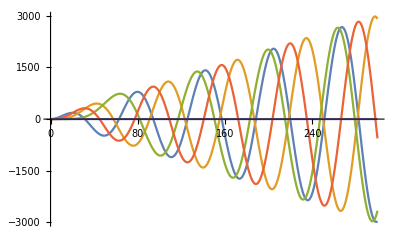

```mathematica
kplot=0.1 ;
Plot[{x^2 SphericalBesselJ[0,kplot x],x^2 SphericalBesselJ[2,kplot x],x^2 SphericalBesselJ[4,kplot x],x^2 SphericalBesselJ[1,kplot x],SphericalBesselJ[2,kplot x]},{x,0,300}]
```

```mathematica
0.690*0.084/2
0.96*0.12/2
Log[Exp[2.72]*0.3]/2
```

0.02898

0.0576

0.758014

```mathematica
0.317*0.94/2
0.690*0.84/2
```

0.14899

0.2898

```mathematica
0.2937-0.286
```